01

牛顿力学 —— 回顾与总结

本章回顾牛顿力学的主要知识背景，内容包括

运动学 (kinetics)：描述运动现象   how

动力学 (dynamics)：揭示运动规律  why

分为以下三节讨论

正交曲线坐标系

牛顿力学基本定律和定理

变质量体系

通过回顾和一些例题，希望能回想起牛顿力学描述运动现象、运动规律的一些常用方法。

同时，管窥拉格朗日力学的可能的起源：偏导数如何进入单质点的运动方程？

## § 1.1 正交曲线坐标系

要描述运动，就需要坐标系。最为熟悉的莫过于直角坐标系。

在直角坐标系中，空间中的任意一点 P 可以用三个直角坐标 (x,y,z) 表征

牛顿力学的研究对象（最简单的质点）所在的位置可以用空间点 P 表示

等价地，也可以用直角坐标系下的位置矢量 r⃗ 描述

r⃗=x (e⃗)_x+y (e⃗)_y+z (e⃗)_z,      位置矢量是从坐标原点到质点所在的点 P 所张的矢量。

为表述方便，以下我们记：x=x_1, y=x_2, z=x_3;         (e⃗)_x=(x̂)_1,  (e⃗)_y=(x̂)_2,   (e⃗)_z=(x̂)_3

从而位置矢量可简写为：

r⃗=x (x̂)_1+y (x̂)_2+z (x̂)_3=(∑_(i=1))^3 x_i (x̂)_i，      {(x̂)_1,(x̂)_2,(x̂)_3}称为笛卡尔坐标（直角坐标）三个基矢量

而任一矢量 A⃗ 在直角坐标中则表为

A⃗=A_x (x̂)_1+A_y (x̂)_2+A_z (x̂)_3=(∑_(i=1))^3 A_i(x̂)_i

其中：A_1=A_x ,  A_2=A_y ,   A_3=A_z  称为矢量 A⃗ 的三个直角坐标分量

以上应该是大家所熟知的。

### § 1.1.1 曲线坐标系

回顾理解曲线坐标系有助于理解广义坐标。

我们试图不求助于作图来理解曲线坐标中的一些概念，正如拉格朗日在给出其力学理论时特别自豪地声称无需作图那样。

如果存在一组独立、连续可微、单值的函数

q_1=f_1(x_1,x_2,x_3),  q_2=f_2(x_1,x_2,x_3),  q_3=f_3(x_1,x_2,x_3)

并且其反函数

x=x_1=(f̃)_1(q_1,q_2,q_3),  y=x_2=(f̃)_2(q_1,q_2,q_3),  z=x_3=(f̃)_3(q_1,q_2,q_3)

也独立、连续可微、单值，

那么 P 点的坐标就也可以用 (q_1,q_2,q_3) 表征，因为 (x_1,x_2,x_3) 与 (q_1,q_2,q_3) 一一对应。

(q_1,q_2,q_3) 称为空间点 P 的曲线坐标。

之所以称为曲线坐标，是因为固定任意两个坐标，变化第三个坐标，映照到原直角坐标系中，通常会得到一条曲线。

用曲线坐标来描述空间任意点位置的坐标系称为曲线坐标系。

典型的曲线坐标系如：

（圆）球坐标系：{x_1=x=r sin θ cos ϕ
x_2=y=r sin θ sin ϕ
x_3=z=r cos θ               {q_1=r=(x^2+y^2+z^2)^(1/2)
q_2=θ=cos^-1 z/r,     ρ=(x^2+y^2)^(1/2)
q_3=ϕ=Piecewise[{{cos^-1 x/ρ,, y≥0}, {2π-cos^-1 x/ρ,, y<0}}]

（圆）柱坐标系：{x=ρ cos ϕ
y=ρ sin ϕ
z=z                       {q_1=ρ=(x^2+y^2)^(1/2)
q_2=ϕ=Piecewise[{{cos^-1 x/ρ,, y≥0}, {2π-cos^-1 x/ρ,, y<0}}]
q_3=z

注意：三个函数独立的要求为：Jacobi 行列式不等于 0。

J=(∂(q_1,q_2,q_3))/(∂(x_1,x_2,x_3))=|(∂q_1)/(∂x_1) | (∂q_1)/(∂x_2) | (∂q_1)/(∂x_3)
(∂q_2)/(∂x_1) | (∂q_2)/(∂x_2) | (∂q_2)/(∂x_3)
(∂q_3)/(∂x_1) | (∂q_3)/(∂x_2) | (∂q_3)/(∂x_3)|≠0

### § 1.1.2 位置矢量在曲线坐标中的表示

在直角坐标系和一般曲线坐标系中，位置矢量 r⃗ 分别表为：

r⃗ = (x̂)_i x_i=r⃗(x_1,x_2,x_3)=r⃗(q_1,q_2,q_3),     (x̂)_1=(e⃗)_x ,  (x̂)_2=(e⃗)_y ,  (x̂)_3=(e⃗)_z 。

这里我们利用了所谓爱因斯坦求和约定，即，对重复指标求和：r⃗ =(∑_(i=1))^3 x_i(x̂)_i   ⟹^记为  x_i (x̂)_i

上式理解为：位置矢量 r⃗ 是坐标的矢量函数。   r⃗ = r⃗(x_1,x_2,x_3)=r⃗(q_1,q_2,q_3)

既然我们引入了曲线坐标 (q_1,q_2,q_3)，矢量特性就不再用( (x̂)_1, (x̂)_2 ,(x̂)_3 ) 这套基矢量来表征。

我们期望有一套新的基矢量。这套新的基矢量如何构造呢？

——   从位置矢量 r⃗ 出发，引入微分线元概念。

由于坐标的微小变化导致位置矢量的变化，称为微分线元 ⅆ r⃗  —— 通过微分线元概念来引入基矢量

显然位置矢量作为坐标的矢量函数是连续可微的，故可将微分线元 ⅆ r⃗ 表为全微分形式

ⅆ r⃗ =(∂r⃗(x_1,x_2,x_3))/(∂x_i)ⅆ x_i= (x̂)_i ⅆ x_i=(∂r⃗(q_1,q_2,q_3))/(∂q_i)ⅆ q_i= (a⃗)_i ⅆ q_i

⟹        ((ⅆ r⃗)^)_ = (x̂)_i ⅆ x_i= (a⃗)_i ⅆ q_i                                              (†)

其中：(∂r⃗(x_1,x_2,x_3))/(∂x_i)= (x̂)_i,         (∂r⃗(q_1,q_2,q_3))/(∂q_i)=(a⃗)_i

因为 r⃗=(x̂)_i x_i 中的 (x̂)_i 为常矢量，故 (∂r⃗(x_1,x_2,x_3))/(∂x_i) 即为直角坐标中三个单位长度的基矢量：( (x̂)_1,(x̂)_2,(x̂)_3)

从 (†) 式类比，很自然地想到，用  (a⃗)_i 做曲线坐标系的基矢量。

现在来看 (a⃗)_i 。先看其方向。以 (a⃗)_1为例，注意到   (x̂)_i 为常矢量，

((a⃗)_1=(∂r⃗(q_1,q_2,q_3))/(∂q_1))_(⏟_定义式)= (∂x_1(q_1,q_2,q_3))/(∂q_1) (x̂)_1+(∂x_2(q_1,q_2,q_3))/(∂q_1)(x̂)_2+(∂x_3(q_1,q_2,q_3))/(∂q_1)(x̂)_3 =(∂x_i)/(∂q_1)(x̂)_i

(a⃗)_1 的几何意义：在空间某点，保持曲线坐标 q_2 和 q_3 不变，仅让坐标 q_1 作一微小变化，

位置矢量函数  r⃗ 相对于 q_1 的变化率。（回过头来想想直角坐标的基矢量是否也是这个意思）

而保持坐标 q_2 和 q_3 不变，仅让坐标 q_1 变化，点 (q_1,q_2, q_3) 在空间的轨迹（跑出的曲线）称为坐标曲线 q_1。

显然，坐标曲线 q_1由下列参数方程给出

{x_1=(f̃)_1(q_1,q_2,q_3)
x_2=(f̃)_2(q_1,q_2,q_3)
x_3=(f̃)_3(q_1,q_2,q_3),   因此坐标曲线 q_1的切向  τ⃗ 为： τ⃗= (∂x_1)/(∂q_1) (x̂)_1+(∂x_2)/(∂q_1)(x̂)_2+(∂x_3)/(∂q_1)(x̂)_3=(a⃗)_1

所以，坐标曲线 q_1的切向就是 (a⃗)_1=(∂r⃗(q_1,q_2,q_3))/(∂q_1) 的方向（此处仅是方向相同，大小尚未归一）。

矢量  (a⃗)_1=(∂r⃗(q_1,q_2,q_3))/(∂q_1)的两个等价意义：{其方向表示坐标曲线 q_1 的切向  τ⃗
保持 q_2, q_3不变，仅让 q_1微变，得到的微分线元ⅆ r⃗=(a⃗)_1 ⅆ q_1

通常，取沿坐标曲线 q_1切向的单位矢量作为曲线坐标系的一个基矢量 (ê)_1，因此，曲线坐标系的三个基矢为：

(ê)_i=((a⃗)_i)/(| (a⃗)_i|)=((a⃗)_i)/h_i,   h_i=| (a⃗)_i|=√(((∂x_1)/(∂q_i))^2+((∂x_2)/(∂q_i))^2+((∂x_3)/(∂q_i))^2),    记得  (a⃗)_i= (∂x_1)/(∂q_i) (x̂)_1+(∂x_2)/(∂q_i)(x̂)_2+(∂x_3)/(∂q_i)(x̂)_3

这里在直角坐标系中利用 勾股 (Pythagorean)定理 求得 (a⃗)_i 的长度 h_i 并进行归一化得 (ê)_i

ⅆ r⃗ = (x̂)_i ⅆ x_i= (a⃗)_i ⅆ q_i=h_i (ê)_i ⅆ q_i,       (a⃗)_i=(x̂)_k(∂^ x_k)/((∂q_i)_)         { (ê)_i, i=1,2,3}   给出新坐标系中的三个基矢量

比较：r⃗ = (x̂)_i x_i≠ h_i q_i  (ê)_i         versus         ⅆ r⃗ = (x̂)_i ⅆ x_i=h_i (ê)_i ⅆ q_i       （隐含对下标 i 求和）

可看到为什么要通过微分线元来引入基矢量，而非从位置矢量本身引入基矢量。

注意曲线坐标系的基矢量  (ê)_i 尽管长度均为 1，但是其方向与空间位置有关，依然是坐标 {q_1,q_2, q_3} 的函数

即：曲线坐标系的基矢  (ê)_i 可能不是常矢量。（尽管其长度已归一化，但方向会随空间位置变。）

这一点不同于直角坐标系，后者的三个基矢 (x̂)_i 都是常矢量。

而这一区别将导致速度、加速度等运动学物理量在曲线坐标系中表达式的复杂性。

接着我们看微分线元 ⅆ r⃗ 的长度，利用直角坐标系中的基矢量满足：

(x̂)_k·(x̂)_k'=δ_(k k')，δ_(k k')={1,    k=k'
0,    k≠k'  —— Kronecker δ 符号，       可得

ⅆ r⃗·ⅆ r⃗=( (x̂)_i ⅆ x_i)·( (x̂)_j ⅆ x_j)=( (x̂)_i· (x̂)_j)ⅆ x_iⅆ x_j=ⅆ_ x_iⅆ x_i    对直角坐标系，结果众所周知
=( (a⃗)_i ⅆ q_i)·( (a⃗)_j ⅆ q_j)      对一般的曲线坐标系
= (a⃗)_i·(a⃗)_jⅆ q_i ⅆ q_j             再利用 (a⃗)_i 表达式
=((∂x_k)/(∂q_i)(x̂)_k)·((x̂)_k'(∂x_k')/(∂q_j))ⅆ q_i ⅆ q_j                 这里是四重求和   i, j, k, k'，记得   (x̂)_k·(x̂)_k'=δ_(k k')
=(∂x_k)/(∂q_i)(∂x_k)/(∂q_j)ⅆ q_i ⅆ q_j=g_(i j)ⅆ q_i ⅆ q_j

g_(i j)= (a⃗)_i·(a⃗)_j=(∂x_k)/(∂q_i)(∂x_k)/(∂q_j)=(∂x_1)/(∂q_i)(∂x_1)/(∂q_j)+(∂x_2)/(∂q_i)(∂x_2)/(∂q_j)+(∂x_3)/(∂q_i)(∂x_3)/(∂q_j),      这里对重复指标 k 求和

g_(i j)构成的 3×3 矩阵称为度规。度规的对角元 g_(i i)=h_i^2    （注意这里  g_(i i) 的两个重复指标 i 不求和）

如果    g_(i j)≡ (a⃗)_i·(a⃗)_j=Piecewise[{{h_i^2,, for  i=j}, {0,, for  i≠j}}]  =h_i^2 δ_(i j) ，则对应的曲线坐标系称为：正交曲线坐标系

对正交曲线坐标系：   ⅆ r⃗·ⅆ r⃗=ⅆ x_iⅆ x_i=h_i^(2^)ⅆ_ q_iⅆ q_i      （注意这里三个重复指标 i  仅对 i  求和一次）

对正交曲线坐标系，总可以对三个两两正交的单位矢量：(ê)_1, (ê)_2, (ê)_3 的下标（编号）进行适当的调整，使得：

(ê)_1×(ê)_2=(ê)_3,  (ê)_2×(ê)_3=(ê)_1,  (ê)_3×(ê)_1=(ê)_2
这种正交曲线坐标系称为右手系。

Take-home message，对正交曲线坐标系，有：

如图：空间中任一点 P ，用三个坐标  q_1, q_2, q_3 描述。
                对应到直角坐标：{q_1
q_2 
q_3     ⟹     {x_1(q_1,q_2,q_3)
(x_2(q_1,q_2,q_3))^
(x_3(q_1,q_2,q_3))^
若^保持坐标 q_2 和 q_3不变，仅让坐标 q_1 变化
          将在空间画出如图红色曲线，称为^坐标曲线 q_1
          曲线在 P 点的切向沿：(a⃗)_1= (∂x_1)/(∂q_1) (x̂)_1+(∂x_2)/(∂q_1)(x̂)_2+(∂x_3)/(∂q_1)(x̂)_3
           位置矢量的微分线元   ⅆ r⃗=(a⃗)_1 ⅆ q_1
若^保持坐标 q_3 和 q_1不变，仅让坐标 q_2 变化
          将在空间画出绿色曲线，称为^坐标曲线 q_2
          曲线在 P 点的切向沿：(a⃗)_2= (∂x_1)/(∂q_2) (x̂)_1+(∂x_2)/(∂q_2)(x̂)_2+(∂x_3)/(∂q_2)(x̂)_3
           位置矢量的微分线元   ⅆ r⃗=(a⃗)_2 ⅆ q_2
若^保持坐标 q_1 和 q_2不变，仅让坐标 q_3 变化
          将在空间画出蓝色曲线，称为^坐标曲线 q_3
          曲线在 P 点的切向沿：(a⃗)_3= (∂x_1)/(∂q_3) (x̂)_1+(∂x_2)/(∂q_3)(x̂)_2+(∂x_3)/(∂q_3)(x̂)_3
          位置矢量的微分线元   ⅆ r⃗=(a⃗)_3 ⅆ q_3    -Graphics3D-

若三矢量：(a⃗)_1, (a⃗)_2, (a⃗)_3 两两相垂直，则称正交曲线坐标系

若三个坐标 q_1, q_2, q_3都发生改变，则微分线元 ⅆ r⃗ 满足

ⅆ r⃗ = (x̂)_i ⅆ x_i= (a⃗)_i ⅆ q_i=h_i (ê)_i ⅆ q_i               (ê)_i=((a⃗)_i)/(| (a⃗)_i|)=((a⃗)_i)/h_i      注：(ê)_i 表达式中的重复指标不求和

ⅆ r⃗·ⅆ r⃗=ⅆ x_iⅆ x_i=g_(i j)ⅆ q_iⅆq_j   ⟹^正交系    h_i^2ⅆ q_iⅆ q_i ,      g_(i j)≡ (a⃗)_i·(a⃗)_j  ⟹^对正交系 Piecewise[{{h_i^2,, i=j}, {0,, i≠j}}]

h_i=[((∂x_1)/(∂q_i))^2+((∂x_2)/(∂q_i))^2+((∂x_3)/(∂q_i))^2]^(1/2)

h_i 的几何意义：

若仅仅让第 i 个坐标 q_i 作微小变化 ⅆ q_i，对应的微分线元长度为：h_i ⅆ q_i    而不是  ⅆ q_i

因此，在正交曲线坐标系中，函数 φ(q_1,q_2,q_3)沿(ê)_i 方向的方向导数为：1/h_i(∂φ)/(∂q_i)  而非 (∂φ)/(∂q_i)。

ⅆ r⃗·ⅆ r⃗ 是什么？

显然，ⅆ r⃗·ⅆ r⃗ 微分线元的长度的平方。微分线元是无穷小量，

因此，坐标 (q_1,q_2,q_3)都发生微小变化 (ⅆ q_1,ⅆ q_2,ⅆ q_3) 时，

位置矢量将划过一小段弧，ⅆ r⃗·ⅆ r⃗为这一小段弧两端的连线（弦）的长度的平方。

微分线元是无穷小量，故ⅆ r⃗·ⅆ r⃗也是这一小段弧的弧长的平方（弧长≈弦长）。所以

(ⅆs)^2=ⅆ r⃗·ⅆ r⃗ =(ⅆx)^2+(ⅆy)^2+(ⅆz)^2 =(∑_(i=1))^3 h_i^2 ⅆ q_iⅆ q_i=(h_1 ⅆ q_1)^2+(h_2 ⅆ q_2)^2+(h_3 ⅆ q_3)^2

这里以 ⅆs 表示一小段弧的弧长。此式对正交曲线坐标系成立

例 1.1.01   code01 .02 3Dcoordinates.nb

对圆柱坐标系：{x=ρ cos ϕ
y=ρ sin ϕ
z=z            取：   (q_1,q_2,q_3)=(ρ,ϕ,z)

有：  {h_1=[((∂x)/(∂ρ))^(2^)+((∂y)/(∂ρ))^2+((∂z)/(∂ρ))^2]^(1/2)=1
h_2=[((∂x)/(∂ϕ))^2+((∂y)/(∂ϕ))^2+((∂z)/(∂ϕ))^2]^(1/2)=ρ
h_3=[((∂x)/(∂z))^2+((∂y)/(∂z))^2+((∂z)/(∂z))^2]^(1/2)=1
 ⟹  { (ê)_1=1/h_1(∂r⃗)/(∂ρ)=(∂x)/(∂ρ) (x̂)_1+(∂y)/(∂ρ)(x̂)_2+(∂z)/(∂ρ)(x̂)_3
=cos ϕ (x̂)_1+sin ϕ (x̂)_2=(ê)_ρ
(ê)_2=1/h_2(∂r⃗)/(∂ϕ)=1/ρ[(∂x)/(∂ϕ) (x̂)_1+(∂y)/(∂ϕ)(x̂)_2+(∂z)/(∂ϕ)(x̂)_3]
     =-sin ϕ (x̂)_1+cos ϕ (x̂)_2=(ê)_ϕ
(ê)_3=1/h_3(∂r⃗)/(∂z)=(∂x)/(∂z) (x̂)_1+(∂y)/(∂z)(x̂)_2+(∂z)/(∂z)(x̂)_3= (x̂)_3=(e⃗)_z-Graphics3D-

显然 (ê)_1, (ê)_2, (ê)_3 两两垂直，构成右手系：(ê)_ρ×(ê)_ϕ=(ê)_z, (ê)_ϕ×(ê)_z=(ê)_ρ, (ê)_z×(ê)_ρ=(ê)_ϕ,

（这就是为何令 q_1=ρ, q_2=ϕ, q_3=z ）

r⃗=x (x̂)_1+y(x̂)_2+z(x̂)_3=ρ (cos ϕ (x̂)_1+sin ϕ(x̂)_2)+z(x̂)_3=ρ (ê)_ρ+z(ê)_z ,

ⅆ r⃗=(∑_(i=1))^3 h_i(ê)_i ⅆ q_i=((ê)_ρ ⅆρ+ρ(ê)_ϕ ⅆϕ)_(⏟_(ⅆ(ρ (ê)_ρ)= (ê)_ρ ⅆρ +ρ ⅆ (ê)_ρ))+(ê)_z ⅆz                    也可以作图得到：ⅆ(ê)_ρ=(ê)_ϕ ⅆϕ

(ⅆs)^2=ⅆ r⃗·ⅆ r⃗=(∑_(i=1))^3(h_i ⅆ q_i)^2=(ⅆρ)^2+(ρⅆϕ)^2+(ⅆz)^2

对圆球坐标系：{x=r sin θ  cos ϕ
y=r sin θ sin ϕ
z=r cos θ              取：(q_1,q_2,q_3)=(r,θ,ϕ)

有：  {h_1=[((∂x)/(∂r))^(2^)+((∂y)/(∂r))^2+((∂z)/(∂r))^2]^(1/2)=1
h_2=[((∂x)/(∂θ))^2+((∂y)/(∂θ))^2+((∂z)/(∂θ))^2]^(1/2)=r
h_3=[((∂x)/(∂ϕ))^2+((∂y)/(∂ϕ))^2+((∂z)/(∂ϕ))^2]^(1/2)=r sin θ
⟹  { (ê)_1=1/h_1(∂r⃗)/(∂r)=(∂x)/(∂r) (x̂)_1+(∂y)/(∂r)(x̂)_2+(∂z)/(∂r)(x̂)_3
=sin θ cos ϕ (x̂)_1+sin θ sin ϕ (x̂)_2+cos θ  (x̂)_3=(ê)_r
(ê)_2=1/h_2(∂r⃗)/(∂θ)=1/r[(∂x)/(∂θ) (x̂)_1+(∂y)/(∂θ)(x̂)_2+(∂z)/(∂θ)(x̂)_3]
     =cos θ cos ϕ (x̂)_1+cos θ sin ϕ (x̂)_2-sin θ  (x̂)_3=(ê)_θ
(ê)_3=1/h_3(∂r⃗)/(∂ϕ)=1/(r sin θ)[(∂x)/(∂ϕ) (x̂)_1+(∂y)/(∂ϕ)(x̂)_2+(∂z)/(∂ϕ)(x̂)_3]
     =-sin ϕ (x̂)_1+cos ϕ (x̂)_2=(ê)_ϕ  -Graphics3D-

显然 (ê)_1, (ê)_2, (ê)_3 两两垂直，构成右手系：(ê)_r×(ê)_θ=(ê)_ϕ, (ê)_θ×(ê)_ϕ=(ê)_r, (ê)_ϕ×(ê)_r=(ê)_θ,

（这就是为何令 q_1=r, q_2=θ, q_3=ϕ 而非  q_2=ϕ, q_3=θ）

r⃗=x (x̂)_1+y(x̂)_2+z(x̂)_3=r (sin θ cos ϕ (x̂)_1+sin θ sin ϕ(x̂)_2+cos θ(x̂)_3)=r (ê)_r ,

ⅆ r⃗=(∑_(i=1))^3 h_i(ê)_i ⅆ q_i= (ê)_r ⅆr+((ê)_θ rⅆθ+(ê)_ϕ r sin θⅆϕ)_(⏟_(ⅆ (ê)_r=(ê)_θ ⅆθ + (ê)_ϕ sin θⅆϕ))                也可以作图得到： ⅆ(ê)_r=(ê)_θ ⅆθ + (ê)_ϕ sin θⅆϕ

(ⅆs)^2=ⅆ r⃗·ⅆ r⃗=(∑_(i=1))^3(h_i ⅆ q_i)^2=(ⅆr)^2+(rⅆϕ)^2+(r sin θⅆϕ)^2

注意我们这里无需作图即可求出正交曲线坐标中：r⃗,  ⅆ r⃗,  (ⅆs)^2  这一系列关系。

\[MathematicaIcon] Mathematica 代码      求得：      (ê)_1=sin θ cos ϕ (x̂)_1+sin θ sin ϕ(x̂)_2+cos θ  (x̂)_3,       (ê)_2=cos θ cos ϕ (x̂)_1+cos θ sin ϕ(x̂)_2-sin θ  (x̂)_3,         (ê)_3=-sin ϕ  (x̂)_1+cos ϕ  (x̂)_2

```mathematica
x=r Sin[θ] Cos[ϕ];      y=r Sin[θ] Sin[ϕ];           z=r Cos[θ];

a1v={D[x,r],D[y,r],D[z,r]};       a2v={D[x,θ],D[y,θ],D[z,θ]};        a3v={D[x,ϕ],D[y,ϕ],D[z,ϕ]};

h0={a1v.a2v,a2v.a3v,a3v.a1v}//FullSimplify         (* 验证 Subscript[g, ij] = 0   ———— 正交曲线坐标系 *)

h1=FullSimplify[(a1v.a1v)^(1/2),{r>0,0≤θ≤π}];
h2=FullSimplify[(a2v.a2v)^(1/2),{r>0,0≤θ≤π}];
h3=FullSimplify[(a3v.a3v)^(1/2),{r>0,0≤θ≤π}];
{h1,h2,h3}

e1v=a1v/h1;             e2v=a2v/h2;                     e3v=a3v/h3;        (* 三个基矢量 *)

{e1v,e2v,e3v}
```

{0,0,0}

{1,r,r Sin[θ]}

{{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]},{Cos[θ] Cos[ϕ],Cos[θ] Sin[ϕ],-Sin[θ]},{-Sin[ϕ],Cos[ϕ],0}}

\[FreakedSmiley]  QUIZ：在力学中为何要引入（利用）基矢量 (ê)_α 随空间位置变化的曲线坐标系（举例说明）

### § 1.1.3 正交曲线坐标中的速度和加速度

回顾前一小节的内容：

位置矢量：r⃗ =r⃗(x_1,x_2,x_3)=r⃗(q_1,q_2,q_3)  视为是曲线坐标 (q_1,q_2,q_3)的矢量函数

三个基矢量：曲线坐标系中的三个基矢量来自 q_α 曲线的切向矢量的归一化

(a⃗)_α=(∂r⃗(q_1,q_2,q_3))/(∂q_α),     (ê)_α=((a⃗)_α)/(|(a⃗)_α|)=((a⃗)_α)/h_α,      |(τ⃗)_α|=h_α

也可视为来自微分线元（位置矢量的全微分）

ⅆ r⃗=(∑_(α=1))^3 (a⃗)_α ⅆ q_α=(∑_(α=1))^3 h_α (ê)_α ⅆ q_α,      h_α (e⃗)_α=(∂r⃗)/(∂q_α)

这里以  (e⃗)_α 表示曲线坐标系的三个基矢量（而非直角坐标基矢量）。

此外，表示矢量分量的下标也改用希腊字母 α,  β,  ...，因为英文字母 i, j, ... 将留做粒子指标。

现在来看速度和加速度。要写成以 (e⃗)_α为基矢量的分量形式。对任意矢量 A⃗=A_α (e⃗)_α=(Ã)_α (x̂)_α，   (x̂)_α为直角坐标基矢

把速度、加速度表示为描述粒子位置的（曲线）坐标、坐标对时间的导数、曲线坐标系基矢量的函数。

即，若 A⃗ 表示速度或加速度，则应写成  A⃗=A_α (e⃗)_α, 其中 A_α 称为矢量 A⃗ 的 α 分量，是坐标及其时间导数的函数。

注意粒子的位置矢量 r⃗ 是  q_α 的矢量函数，与  (q̇)_α 无关，α=1,2,3

速度：v⃗≡r^OverDot[⇀]≡(ⅆ r⃗)/ⅆt=(∑_(α=1))^3 (∂r⃗)/(∂q_α)(ⅆ q_α)/ⅆt=(∑_(α=1))^3 h_α (ê)_α(q̇)_α=(∑_(α=1))^3(h_α (q̇)_α)_(⏟_v_α)(ê)_α=(∑_(α=1))^3 v_α (ê)_α=v⃗(q_α, (q̇)_α),  是 q_α 和  (q̇)_α 的函数

v⃗=(∑_(α=1))^3 v_α (ê)_α ,       v_α=h_α (q̇)_α            容易理解：因为 q_α 微变，微分线元为  (h_α ⅆ q_α)(ê)_α

在曲线坐标中，矢量特性均用三个基矢量  (ê)_α 来表征，不再表为 x,y, z 三个直角坐标分量

因而三个速度分量    v_α=h_α (q̇)_α，是 q_α 和  (q̇)_α 的函数（因为 h_α 依赖于 q_α）

注意：我们有                                   v⃗=(∑_(α=1))^3 v_α (ê)_α,    其中    v_α=h_α (q̇)_α            但：r⃗≠(∑_(α=1))^3 q_α(ê)_α     尽管  q_α 是坐标

比较直角坐标系中：    v⃗=(∑_(α=1))^3 v_α (x̂)_α,   其中    v_α=(ẋ)_α,                        r⃗=(∑_(α=1))^3 x_α(x̂)_α         此式仅在直角坐标系中成立

\[FreakedSmiley]  QUIZ：位置矢量写成曲线坐标系下的三个分量形式是什么样子的？   r⃗=(∑_(α=1))^3 r_α(ê)_α            r_α= ？

速率平方：(v⃗)^2=v⃗·v⃗=(∑_(α=1))^3 h_α^2 (q̇)_α^2  =v_x^2+v_y^2+v_z^2    当然也是 q_α 和  (q̇)_α 的函数（注意  (ê)_α 对正交曲线坐标系是两两垂直的）

速度表达式应较易理解，v_α=h_α (q̇)_α，  v⃗=(∑_(α=1))^3 v_α (ê)_α。  比较以下梯度表达式

比较 |          直角坐标 x_α |                       正交曲线坐标 q_α
速度分量： |                   v_α=(ẋ)_α |                             v_α=h_α (q̇)_α                           v⃗=(∑_(α=1))^3 v_α (ê)_α=(∑_(α=1))^3 h_α(q̇)_α (ê)_α
梯度分量： |            (∇φ)_α=(∂φ)/(∂x_α) |                          (∇φ)_α=1/h_α(∂φ)/(∂q_α)               ∇φ=(∑_(α=1))^3(∇φ)_α (ê)_α=(∑_(α=1))^3 1/h_α(∂φ)/(∂q_α) (ê)_α

加速度：a⃗≡v^OverDot[⇀]=(ⅆ v⃗)/ⅆt=r^(⇀^(..))   ⟹^记为(∑_(α=1))^3 a_α (ê)_α       正交曲线坐标系中的各个加速度分量：a_α,    α=1,2,3

加速度的 α 分量 a_α 是所有坐标及其时间导数的函数

接着我们来求三个加速度分量 a_α 的表达式。

直接将 v⃗=(∑_(α=1))^3 v_α (ê)_α=(∑_(α=1))^3 h_α (q̇)_α(ê)_α 对 t 求导，因为 h_α, (q̇)_α, (ê)_α 都是 q_α(t)的函数，都需求导，过于复杂。

为此，将等式    (ⅆ v⃗)/ⅆt=(∑_(β=1))^3 a_β (ê)_β      两边同乘以 (ê)_α 并记得  (ê)_α=1/h_α(∂r⃗)/(∂q_α)  是正交归一基矢量  (ê)_α· (ê)_β=δ_αβ，可得：

加速度分量   a_α=(1/h_α(∂r⃗)/(∂q_α))_(⏟_((ê)_α))·(ⅆ v⃗)/ⅆt             即：h_α a_α=(∂r⃗)/(∂q_α)·(ⅆ v⃗)/ⅆt=ⅆ/ⅆt(v⃗·(∂r⃗)/(∂q_α))- v⃗· ⅆ/ⅆt(∂r⃗)/(∂q_α)

h_α a_α=ⅆ/ⅆt(v⃗·(∂r⃗)/(∂q_α))-v⃗· ⅆ/ⅆt(∂r⃗)/(∂q_α)

利用：{(∂r⃗)/(∂q_α)=(∂OverDot[r⃗])/(∂(q̇)_α)=(∂v⃗)/(∂(q̇)_α)           点点消
ⅆ/ⅆt(∂r⃗)/(∂q_α)=(∂OverDot[r⃗])/(∂q_α)=(∂v⃗)/(∂q_α)    对坐标偏导与对时间全导交换次序？ （稍后会给出证明）

可得：v⃗·(∂r⃗)/(∂q_α)=v⃗·(∂v⃗)/(∂(q̇)_α)=(∂(v⃗·v⃗/2))/(∂(q̇)_α)

从而：h_α a_α=ⅆ/ⅆt(v⃗·(∂v⃗)/(∂(q̇)_α))-v⃗· (∂v⃗)/(∂q_α)=ⅆ/ⅆt[(∂((v⃗)^2/2))/(∂(q̇)_α)]- (∂((v⃗)^2/2))/(∂q_α)

所以：   a_α=(((1/h_α[ⅆ/ⅆt∂/(∂(q̇)_α)((v⃗)^2/2)- ∂/(∂q_α)((v⃗)^2/2)])^)_)^            求加速度中出现偏导数，偏导数进入运动方程

•  比较力学课推导过的

a⃗=(a⃗)_t+(a⃗)_n=ⅆv/ⅆt τ⃗+v^2/ρ n⃗

其中 τ⃗ 和 n⃗ 分别为质点运动曲线的切向和法向，

故 (1.EquationNumbered)式常用于讨论约束在确定曲线上的质点运动（在所谓自然坐标系中处理问题），

而 (1.EquationNumbered) 式则用于任意正交曲线坐标系。

\[FreakedSmiley]   公式 (1.EquationNumbered) 把加速度分量表示为 (v⃗)^2 的偏导？ 相比于式 (1.EquationNumbered)，有何益处？

可在任意坐标（如直角坐标）下求得标量：(v⃗)^2(x,y,z,ẋ,ẏ,ż)  —— 标量化

再利用坐标变换：{x_α=x_α(q_1,q_2,q_3)
(ẋ)_α=(ẋ)_α(q_1,q_2,q_3,(q̇)_1,(q̇)_2,(q̇)_3) 化为曲线坐标 q 的函数：(v⃗)^2(q_1,q_2,q_3,(q̇)_1,(q̇)_2,(q̇)_3)

最后代入同一个公式 即求得任意坐标下的加速度分量。

这样做的好处是无需将 ⅆ r⃗在不同坐标下分解为不同分量形式 —— 矢量力学标量化！

💡  既然加速度 a⃗ 可以这么做，那么牛顿方程 F⃗=m a⃗ 能否也这么做，就是三步走

标量化，化为任意曲线坐标 q 的函数，代入同一个公式（形式不依赖于坐标系的公式）

—— “人民有信仰，国家有力量，民族有希望”     ——   力学新形式   ——    “心有所信，方能行远。”

Jesus said unto him,If thou canst believe,all things are possible to him that believeth.   ——  Mark 9:23

注意加速度分量 a_α 表达式中，中括号内的形式：ⅆ/ⅆt∂/(∂(q̇)_α)- ∂/(∂q_α)        ——  拉格朗日方程正是这个形式

对于矢量力学，运动方程在不同坐标系中形式迥异：

直角坐标：{F_x=m x^(..)
F_y=m y^(..)
F_z=m z^(..)                 球坐标：{F_r=m a_r=m ( r^(..)-r(θ̇)^2-r sin^2 θ (ϕ̇)^2)
F_θ=m a_θ=m (2 ṙ θ̇+r θ^(..)-r sinθ cosθ (ϕ̇)^2)
F_ϕ=m a_ϕ=m (r ϕ^(..)sin θ+2 ṙ ϕ̇ sin θ+2r θ̇ ϕ̇ cos θ)

因此人们希望有一个形式不依赖于坐标系的牛顿方程

思考：既然直角坐标形式最简单，为何还要取其它坐标？（例：在球面上运动的质点）

💡  既然如此，让我们提早感受一下这“看上去很美”的感觉 —— 运动方程在不同坐标系中具有相同的形式。

牛顿方程矢量形式： F⃗=m a⃗

⟹^任意正交曲线坐标系    F_α=m a_α=(((1/h_α[ⅆ/ⅆt∂/(∂(q̇)_α)((m(v⃗)^2)/2)- ∂/(∂q_α)((m(v⃗)^2)/2)])^)_)^     注意右边加速度已“标量化”

动能：T=(m(v⃗)^2)/2      (⟹^如果是保守力)_(F⃗=-∇U)   -(∇U)_α=(((1/h_α[ⅆ/ⅆt(∂ T)/(∂(q̇)_α)- (∂ T)/(∂q_α)])^)_)^        再利用正交曲线坐标系的梯度公式

⟹^((∇U)_α= 1/h_α(∂U)/(∂q_α))    -1/h_α(∂U)/(∂q_α)=(((1/h_α[ⅆ/ⅆt∂/(∂(q̇)_α)T- ∂/(∂q_α)T])^)_)^

⟹^(如果势能 U 与 (q̇)_α 无关)          ⅆ/ⅆt∂/(∂(q̇)_α)(T-U)- ∂/(∂q_α)(T-U) =0

⟹^(L=T-U)  ⅆ/ⅆt(∂L)/(∂(q̇)_α)- (∂ L)/(∂q_α) =0     —— 与坐标无关的“牛顿方程”，即拉格朗日方程，

L =T-U  称为拉格朗日量

当然，以上推导中做了许多假设（思考：做了哪些假设？）

质量不变、正交曲线坐标系、保守力、势能与 (q̇)_α 无关、单质点、点点消、偏导全导对调

拉格朗日在更一般的情况下导出拉格朗日方程。规避所有这些假设或推广其适用范围

怎么求 L？因为 T 与 U 是标量，可在直角坐标下求，再经“坐标变换”：x_α(q_α),  (ẋ)_α(q_α,(q̇)_α)即可。

现在，回过头来证明上述紫色和绿色两个等式 (1.EquationNumbered)

(∂r⃗)/(∂q_α)=(∂OverDot[r⃗])/(∂(q̇)_α)=(∂v⃗)/(∂(q̇)_α) 的证明

注意 v⃗≡r^OverDot[⇀]=(∑_(β=1))^3 h_β (ê)_β(q̇)_β  是 q_α 和  (q̇)_α 的函数，而 r⃗ , (ê)_α 和 h_α 均仅为 q_α 的函数，不依赖于 (q̇)_α

从等式右边出发：我们有

(∂v⃗)/(∂(q̇)_α)=∂/(∂(q̇)_α)[(∑_(β=1))^3 h_β(q̇)_β (ê)_β]=(∑_(β=1))^3 h_β (ê)_β(∂(q̇)_β)/(∂(q̇)_α)=(∑_(β=1))^3 h_β (ê)_β δ_(α β)=h_α (ê)_α=(∂r⃗)/(∂q_α)

这里利用了 r⃗ 仅为 q_α 的函数，因而 h_α (ê)_α=(∂r⃗)/(∂q_α)也仅为 q_α 的函数，与 (q̇)_α 无关

这个等式在 q_α 表示广义坐标且约束不显含广义速度时仍然成立（见下一章）。

此等式俗称：“点点消” (dot cancellation)，有诗为证：“著雨胭脂点点消，半开时节最妖娆”

ⅆ/ⅆt(∂r⃗)/(∂q_α)=(∂OverDot[r⃗])/(∂q_α)=(∂v⃗)/(∂q_α) 的证明

还是利用 r⃗ 仅为 q_α 的函数，(∂r⃗)/(∂q_α)也只是 q_α 的函数，不显含 t，不依赖于 (q̇)_α，因此

ⅆ/ⅆt(∂r⃗)/(∂q_α)=(∑_(β=1))^3 ∂/(∂q_β)((∂r⃗)/(∂q_α))(q̇)_β=(∑_(β=1))^3 ∂/(∂q_α)((∂r⃗)/(∂q_β))(q̇)_β=(∑_(β=1))^3 ∂/(∂q_α)((∂r⃗)/(∂q_β) (q̇)_β)
=∂/(∂q_α)(∑_(β=1))^3 ((∂r⃗)/(∂q_β))(q̇)_β=∂/(∂q_α)(ⅆ r⃗)/ⅆt=(∂v⃗)/(∂q_α)

在 q_α 表示广义坐标时，尽管 r⃗ 不仅依赖于 q_α，还可能显含时间 t，但仍有相似的等式（见下一章）

例 1.1.02  球坐标系中的速度、加速度表示

球坐标：h_r=1,   h_θ=r,  h_ϕ=r sin θ,     记得：  v_α=h_α (q̇)_α

故：v_r=ṙ,    v_θ=r θ̇,    v_ϕ=r sin θ ϕ̇,

v⃗=ṙ (ê)_r+r θ̇ (ê)_θ+r sin θ ϕ̇ (ê)_ϕ,

v^2=(ṙ)^2+r^2(θ̇)^2 +r^2 sin^2 θ (ϕ̇)^2  （因为是正交曲线坐标，可用 Pythagorean 定理）

利用等式 (1.EquationNumbered) ：     a_α=(((1/h_α[ⅆ/ⅆt∂/(∂(q̇)_α)((v⃗)^2/2)- ∂/(∂q_α)((v⃗)^2/2)])^)_)^

a_r=1/(2 h_r)[ⅆ/ⅆt((∂v^2)/(∂ṙ))-(∂v^2)/(∂r)]=r^(..)-r(θ̇)^2-r sin^2 θ (ϕ̇)^2

a_θ=1/(2 h_θ)[ⅆ/ⅆt((∂v^2)/(∂θ̇))-(∂v^2)/(∂θ)]=1/r[(ⅆ(r^2 θ̇))/ⅆt]-r sinθ cosθ (ϕ̇)^2
=2 ṙ θ̇+r θ^(..)-r sinθ cosθ (ϕ̇)^2

a_ϕ=1/(2 h_ϕ)[ⅆ/ⅆt((∂v^2)/(∂ϕ̇))-(∂v^2)/(∂ϕ)]=1/(r sin θ)[(ⅆ(r^2 sin^2 θ ϕ̇))/ⅆt]
=r ϕ^(..)sin θ+2 ṙ ϕ̇ sin θ+2r θ̇ ϕ̇ cos θ

例1.1.03  柱坐标系中的速度、加速度表示

柱坐标：h_ρ=1,   h_ϕ=ρ,  h_z=1,    从    v_α=h_α (q̇)_α   出发

得：v_r=ρ̇,    v_θ=ρ ϕ̇,    v_z= ż,

v⃗=ρ̇ ϕ̇ (ê)_ϕ+ ż (ê)_z,

v^2=(ρ̇)^2+ρ^2(ϕ̇)^2 + (ż)^2

a_ρ=1/(2 h_ρ)[ⅆ/ⅆt((∂v^2)/(∂ρ^•))-(∂v^2)/(∂ρ)]=ρ^(..)-ρ(ϕ̇)^2

a_ϕ=1/(2 h_ϕ)[ⅆ/ⅆt((∂v^2)/(∂ϕ^•))-(∂v^2)/(∂ϕ)]=2 ρ̇ ϕ̇+ρ ϕ^(..)

a_z=1/(2 h_z)[ⅆ/ⅆt((∂v^2)/(∂z^•))-(∂v^2)/(∂z)]=z^(..)

##### \[MathematicaIcon] Mathematica code 柱坐标 （试写一个球坐标中求速度加速的的代码）

```mathematica
Quit
```

```mathematica
er={ Cos[ϕ[t]], Sin[ϕ[t]],0};
eϕ={- Sin[ϕ[t]], Cos[ϕ[t]],0};
ez={0,0,1};
rv[t_]:={r[t]Cos[ϕ[t]],r[t]Sin[ϕ[t]],z[t]};
vv[t_]:=D[rv[t],t]
av[t_]:=D[vv[t],t]
```

```mathematica
Simplify[(vv[t].er)]
Simplify[(vv[t].eϕ)]
Simplify[(vv[t].ez)]
```

r'[t]

r[t] ϕ'[t]

z'[t]

```mathematica
Simplify[(av[t].er)]
Simplify[(av[t].eϕ)]
Simplify[(av[t].ez)]
```

-r[t] ϕ'[t]^2+r''[t]

2 r'[t] ϕ'[t]+r[t] ϕ''[t]

z''[t]

##### 复数之妙

例1.1.04  平面极坐标系中的速度、加速度表示 —— 复数之妙

平面极坐标相当于柱坐标中的 z=ż=0

故由上题可得速度、加速度分量：

v⃗=ρ̇ (ê)_ρ+ρ ϕ̇ (ê)_ϕ

a_ρ=ρ^(..)-ρ(ϕ̇)^2,               a_ϕ=2 ρ̇ ϕ̇+ρ ϕ^(..)

另外，由复数也可以方便地导出极坐标系的速度、加速度分量

对平面，位置矢量可以用复数  ρ ⅇ^(ⅈ ϕ) 表示（复数的指数表示和几何表示）

比较位置矢量在极坐标下的形式：ρ(ê)_ρ，可知

用复数 ρ ⅇ^(ⅈ ϕ)表示一个矢量，位置矢量 ρ(ê)_ρ 的方向由  ⅇ^(ⅈ ϕ)确定，故，ⅇ^(ⅈ ϕ) 对应于 (ê)_ρ

复数知识表明，ⅈ ⅇ^(ⅈ ϕ) 是 ⅇ^(ⅈ ϕ)逆时针旋转 90度，因而 ⅈ ⅇ^(ⅈ ϕ) 对应于 (ê)_ϕ

有了这两个对应，我们就可以很方便地导出平面极坐标系中的速度、加速度表示

位置矢量   r⃗=ρ (ê)_ρ= ρ ⅇ^(ⅈ ϕ)      用复数表示

速度：(ⅆ r⃗)/ⅆt=(ⅆ(ρ ⅇ^(ⅈ ϕ)))/ⅆt=ρ̇ ⅇ^(ⅈ ϕ)+ρ ⅈ ⅇ^(ⅈ ϕ)ϕ̇=ρ̇(ê)_ρ+ρ ϕ̇(ê)_ϕ

加速度：(ⅆ^2 r⃗)/(ⅆ t^2)=ⅆ/ⅆt((ⅆ r⃗)/ⅆt)=ⅆ/ⅆt(ρ̇ ⅇ^(ⅈ ϕ)+ρ ⅈ ⅇ^(ⅈ ϕ)ϕ̇ )
=ρ^(..)ⅇ^(ⅈ ϕ)+ρ̇ ⅈ ⅇ^(ⅈ ϕ)ϕ̇+ρ̇ ⅈ ⅇ^(ⅈ ϕ)ϕ̇-ρ ⅇ^(ⅈ ϕ)(ϕ̇)^2+ρ ⅈ ⅇ^(ⅈ ϕ)ϕ^(..)
=ρ^(..)ⅇ^(ⅈ ϕ)-ρ ⅇ^(ⅈ ϕ)(ϕ̇)^2+ρ̇ ϕ̇ ⅈ ⅇ^(ⅈ ϕ)+ρ̇ ϕ̇ ⅈ ⅇ^(ⅈ ϕ)+ρ ϕ^(..) ⅈ ⅇ^(ⅈ ϕ)
=(ρ^(..)-ρ (ϕ̇)^2) ⅇ^(ⅈ ϕ)+(2 ρ̇ ϕ̇+ρ ϕ^(..) )ⅈ ⅇ^(ⅈ ϕ)
=(ρ^(..)-ρ (ϕ̇)^2)(ê)_ρ+(2 ρ̇ ϕ̇+ρ ϕ^(..) )(ê)_ϕ

哇塞！推导简单多了。复数真妙哉，物理多有赖，欲窥其全貌，《数理》来搬柴。

复数的确很妙，但只能处理二维问题，三维体系有没有类似的处理方法？

复数由一对有序实数构成，
如果把复数看成二元数，
能否构造三元数处理三维问题？不能。
复数的推广是 Hamilton 的四元数。
就是和太太在 Broome 桥散步时神游物外
            悟出其乘法定义的四元数。
而Hamilton在他生命的最后二十年，
除了和太太吵架，几乎专注于四元数的研究。
遗憾的是，四元数在物理上尚未有广泛的应用。-Graphics-

——  要不是常和太太吵架，Hamilton 说不定能在四元数上有更大的作为

### § 1.1.4 自然坐标系

理解自然坐标系有助于理解约束与广义坐标。

当粒子运动轨道给定情况下，描述粒子的位置就不再需要三个坐标参数 (q_1,q_2,q_3)

三维空间的一条曲线需要两个方程来确定，
因而当粒子运动轨道给定时,
描述粒子位置的三个坐标参数 (q_1,q_2,q_3)
满足了空间曲线的两个方程，因此
三个坐标参数 (q_1,q_2,q_3) 中仅一个独立。
仅需要一个参数就可以确定粒子位置
                      ——   故称为一个自由度
这个参数可选为：（如图）
从确定的参考点 O_s（相当于坐标原点）
到质点所在位置的有向弧长 s （红色曲线）-Graphics-

称为：自然坐标系，也称为 弧线坐标。s 确定，粒子坐标就确定，s 是一种广义坐标

何谓广义坐标：与质点坐标（位置）能建立一一对应关系的量 ——  一个不太严谨的定义

以下我们推导使用弧线坐标时，质点速度、加速度的表达式。出发点依然是：位置矢量看成坐标的矢量函数。

显然，在自然坐标系（弧线坐标）中，质点位置矢量 r⃗ 是弧线坐标 s 的函数：r⃗(s)

——  总是把位置矢量写成“坐标”的矢量函数

微分线元 (位置矢量的微分 ) ⅆ r⃗=lim_(Δ t→ 0) Δ r⃗ 的长度等于弧长微分 ⅆs=lim_(Δ t→ 0) Δ s

即：|ⅆs|=|ⅆ r⃗|   ⟹   |(ⅆ r⃗)/ⅆs|=1

定义：(ⅆ r⃗)/ⅆs=τ⃗,   τ⃗ 为轨道曲线在质点位置处的切向，|τ⃗|=|(ⅆ r⃗)/ⅆs|=1

速度：v⃗=(ⅆr⃗(s))/ⅆt=(ⅆr⃗(s))/ⅆs ⅆs/ⅆt=τ⃗ v,      其中：v=ⅆs/ⅆt 为速率

上式表明，速度沿轨道曲线切向 τ⃗，而 τ⃗ 指向 s 增加的方向

加速度：a⃗=(ⅆ v⃗)/ⅆt=ⅆ/ⅆt(v τ⃗)=v̇ τ⃗+v (ⅆ τ⃗)/ⅆt

注意到 τ⃗ 和 r⃗ 都是弧线坐标 s 的函数（总是看成坐标的函数）。

(ⅆ τ⃗)/ⅆt=(ⅆτ⃗(s))/ⅆs ⅆs/ⅆt=|(ⅆ τ⃗)/ⅆs|n⃗  v              以下证明(ⅆτ⃗(s))/ⅆs 的方向 n⃗ 垂直于 τ⃗

因为  τ⃗·τ⃗=1    ⟹    ⅆ/ⅆs(τ⃗·τ⃗)=0   ⟹  τ⃗·((ⅆ τ⃗)/ⅆs)_(⏟_(κ̃ n⃗))=0    ⟹    τ⃗·κ̃ n⃗=0

n⃗ 垂直于 τ⃗，称为主法向单位矢量。κ̃ 为 (ⅆ τ⃗)/ⅆs 的长度 |(ⅆ τ⃗)/ⅆs|。

此外，从图中可以看到，n⃗ 指向曲线内凹法向。

最后，看(ⅆ τ⃗)/ⅆs 的长度 |(ⅆ τ⃗)/ⅆs|= κ̃ 
 κ̃ =|(ⅆ τ⃗)/ⅆs|=lim_(Δs→ 0) (|Δ τ⃗|)/(|Δs|)=lim_(Δs→ 0) (|τ⃗||Δθ|)/(|Δs|)  
                     =lim_(Δs→ 0) (|Δθ|)/(|Δs|)=ρ=1/R,
Δθ  是 τ⃗  在弧线坐标微变时，转过的角度 ， 
ρ 和 R 分别为曲率和曲率半径-Graphics-

即：(ⅆ τ⃗)/ⅆs=(n⃗)/R ,     n⃗  垂直于 τ⃗
综上：a⃗=v̇ τ⃗+v (ⅆ τ⃗)/ⅆt=v̇ τ⃗+v^2/R n⃗   
或：{a_τ=v̇           切向加速度对应速度大小变化   
a_n=v^2/R       法向加速度对应速度方向变化  -Graphics-

自然坐标下的加速度公式：     a⃗=v̇ τ⃗+(v^(2^))/R_ n⃗             密切面：由 M, A, N 三点构成的平面 (M→A, N→A)
切向：OverVector[AM] 方向或 OverVector[NA]方向 (M→A, N→A)
切向在密切面内
思考：图中切向能定义为 OverVector[MA] 或 OverVector[AN] 方向吗？
主法向：在密切面内且垂直于切向的方向

思考：我们推导得到 (ⅆ τ⃗)/ⅆs=(n⃗)/R ,     n⃗  垂直于 τ⃗，为什么 n⃗ 沿密切面和法面的交线?

τ⃗ 的方向平行于 AM 和 AN (M→A, N→A)，故  n⃗ 在过 AM 和过 AN 的平面上，也就是在密切面上。

##### 空间曲线的一些基本概念：(skip)

密切面是三点 A,M,N 确定的平面，再令 M, N →A

切向是连接 A 和 M 的直线并沿 s 增大的方向，再令  M→A

\[FreakedSmiley]  QUIZ：n⃗ 垂直于 τ⃗，而落在曲线法面上的任一直线均垂直于 τ⃗，如何确定 n⃗ ？

n⃗ 落在密切面上。

τ⃗=(ⅆ r⃗)/ⅆs,         (ⅆ τ⃗)/ⅆs=ρ n⃗,      b⃗≡τ⃗×n⃗，    (ⅆ b⃗)/ⅆs=-κ n⃗,      (ⅆ n⃗)/ⅆs=-ρ τ⃗+κ b⃗

这四个式子称为Seret-Frenet公式

注意 ρ≥0,  κ 可正可负。对平面曲线 κ=0，b⃗ 垂直于曲线所在的平面

\[FreakedSmiley]  试证明Seret-Frenet 公式并验证以下公式

若令：(g⃗)_1=τ⃗, (g⃗)_2=n⃗, (g⃗)_3=b⃗,  则有： (ⅆ(g⃗)_k)/ⅆs=ω⃗×(g⃗)_k，其中： ω⃗=κ τ⃗+ρ b⃗

对 V⃗ 为一般矢量：V⃗=V_t τ⃗+V_n n⃗+V_b b⃗，则

(ⅆ V⃗)/ⅆs=((ⅆ V_t)/ⅆs τ⃗+(ⅆ V_n)/ⅆs n⃗+(ⅆ V_b)/ⅆs b⃗ )+ω⃗×V⃗

参阅：Johns  “Analytical Mechanics for Relativity & Quantum Mechanics”  2nd ed. Oxford Univ. Press 2011

例题 1.1.05：

如图质点沿抛物线轨道 y=x^2/(2p)自A向B运动，切向加速度与法向加速度之比为常数C

求质点在 A,B 两处的速率之比。A , B 两点的坐标分别为  (±p,p/2)

解：

取自然坐标系，加速度公式为：   a⃗=v̇ τ⃗+v^2/R n⃗

a_τ/a_n=(v̇)/(v^2/R) =R/v^2 ⅆv/ⅆt=R/v^2 ⅆv/ⅆs ⅆs/ⅆt=R/v ⅆv/ⅆs
   总要表示为坐标的函数，
   ⅆv/ⅆt=ⅆv/ⅆs ⅆs/ⅆt，再利用：ⅆs/ⅆt=v
R=ⅆs/ⅆθ, 其中 θ 是切向与 x 轴夹角
故：a_τ/a_n=R/v ⅆv/ⅆs=1/v ⅆv/ⅆθ=C
ⅆv/v=Cⅆθ       -Graphics-

∫_v_A^v_B ⅆv/v=C∫_θ_A^θ_B ⅆθ,        因为  θ 是切向与 x 轴夹角， tan θ=y'=x/p

(两边同时积分：ln v_^|)_v_A^v_B=C(θ_B-θ_A)         ⟹      v_B/v_A=ⅇ^(C π/2)               (†)

其中：(θ_B-θ_A) 表示沿抛物线从 A 点到达 B 点，切线方向 τ⃗ 转过的角度，切向沿 s 增方向

同时需要 s 增加时 θ 增加，以保证 R=ⅆs/ⅆθ>0。故从 A 点到 B 点 ⅆθ 是增加的。

这里要动态地理解 (θ_B-θ_A) ，参见 角度变化动态图

\[FreakedSmiley] 思考：如果从 A  开始以初速 v_0 滑到 B，由(†)式， v_B=v_0 ⅇ^(C π/2)，反过来

如果从 B  开始以初速 v_0 滑到 A，那么  v_A=v_0 ⅇ^(- C π/2)  或  v_A=v_0 ⅇ^(+ C π/2)   ???

切向取 s 增加方向，并要保证 R=ⅆs/ⅆθ>0，同时约定速率 v=ⅆs/ⅆt>0

## § 1.2 牛顿力学基本定律和定理

本节回顾质点动力学的基本原理，适用于宏观物体、弱引力情形的低速机械运动。

我们将按以下思路回顾、总结

从物理规律来看：{动量定律
角动量定律
功-能定理

从体系来看：  {单质点

质点系  { 实验室坐标系
质心系

### § 1.2.1 若干概念和定律回顾

绝对时空

牛顿认为，所有运动，日月星辰、车水马龙、云卷云舒、花开花落，均发生于一个绝对空间中，这个空间称为物理空间。

人们可以在这个空间建立一个坐标系(如直角坐标系)，用坐标系（坐标）来描述物体的运动。坐标系与物体运动无关。

另一方面，时间也是绝对的，也与物体的运动无关，牛顿将时间比作沿直线稳恒运动的数学点。

物体的运动，就以表征物体位置的坐标或位置矢量随时间的变化来描述。

牛顿认为，这个坐标系是存在的，称之为惯性坐标系。

相对于这个惯性坐标系做匀速直线运动的坐标系也是惯性系。

不同惯性系之间是伽利略变换。so far so good until ...  （相对论）

质点

质点是一个理想模型，模型忽略了物体形状、大小和内部运动，将物体视为有一定质量的点，以突出其质量与整体位置。

以下若无特别指出，暂时先把物体均视为质点（略去大小、形状和内部运动）

Quiz：有限大小的物体应该视为许多“质点”构成的体系，为什么这些质点的运动可以用单一个质点描述？

在绝对时空的惯性系中，质点的运动满足牛顿三大定律

第一定律：不受外力作用的质点保持静止或匀速直线运动状态

第一定律建立了力、惯性的概念，指出静止与匀速直线运动等价

第一定律实质也可视为定义惯性系（第一定律成立的参考系），断言其存在，等价于动量守恒定律

第二定律：质点运动状态的改变（动量的变化率）正比于作用于质点上的力：F⃗=(ⅆ (m v⃗))/ⅆt

力（可通过其产生的形变程度比较）与其所引起的加速度之比，与力的大小无关，由物体完全确定

| a⃗|/| F⃗|只由物体确定 （线性关系）

第二定律仅适用于惯性系；牛顿力学中，m 是常量，故有：F⃗=m(ⅆ v⃗)/ⅆt=m a⃗=(ⅆ(m v⃗))/ⅆt

F⃗ 和 m 不依赖于不同的惯性系

第三定律：质点的作用总是相互的，作用力与反作用力方向均沿两质点连线上，大小相等，方向相反。

用公式表示：(f⃗)_(i j)=-(f⃗)_(j i)，(r⃗)_(i j)×(f⃗)_(i j)=0.  其中 (f⃗)_(i j) 表示质点 j 对质点 i 的作用力，(r⃗)_(i j)=(r⃗)_i-(r⃗)_j 为从 j 到 i 的矢量

第三定律的弱形式：(f⃗)_(i j)=-(f⃗)_(j i)；第三定律的强形式：(f⃗)_(i j)=-(f⃗)_(j i) 且  (r⃗)_(i j)×(f⃗)_(i j)=0

相互作用以有限速度传播，因此第三定律仅在物体运动速度远低于相互作用传播速度时近似成立

例如相距一定距离的两个运动点电荷之间的相互作用力是不等的。物理理解非常简单。

因为电荷运动，相对位置随时间改变，相互作用力也随时间改变。

第三定律显然应该是同一时刻的相互作用力相等，燃鹅，燃鹅，

相对论告诉我们，“同时”是有相对性的，也就是在实验室观察是“同时”，换个坐标系未必同时，

因此，这就相当于在比较不同时刻的作用力与反作用力，当然未必满足第三定律。

牛顿三定律构成经典力学的基础。

第二、三定律涉及到相互作用的概念，也就是力的概念。目前人们发现自然界有四种相互作用力。

四种相互作用力：强力、弱力、电磁力、引力

强力和弱力只在微观世界起作用，而引力和电磁力经典力学研究的作用力

摩擦力、弹性力等是电磁力的宏观表现

既然相对于绝对空间参考系作匀速直线运动的参考系也是惯性系，不同惯性系之间如何变换？

惯性系之间的伽利略变换

{r⃗'=r⃗-(v⃗)_0 t
t'=t   ⟹   (ⅆ r⃗')/ⅆt=(ⅆ r⃗)/ⅆt-(v⃗)_0
                   (v⃗)_0 为 S'(x'-y'-z')相对于 S (x-y-z)的运动速度       
⟹   v⃗'=v⃗-(v⃗)_0
⟹   a⃗'=a⃗
经典力学中力在变换下不变：  F⃗'=F⃗
F⃗'=m a⃗'    vs    (F⃗)_=m a⃗
⟹  力学相对性原理_：
           力学定律在不同惯性系中形式相同      -Graphics-

一切惯性系等价，无法通过力学实验区分哪个更基本。

——  这里导出力学相对性原理的基础是：长度、时间、力和质量是变换的不变量

在相对论中，物理规律的相对性原理是一个公理性假设。

非惯性系  ——  惯性力

非惯性系中牛顿第二定律不成立。

为了使非惯性系的运动方程与牛顿方程形式上一致，人们引入虚拟的惯性力

惯性系 S：F⃗=m a⃗

非惯性系 S'： v⃗'=v⃗-(v⃗)_0， (v⃗)_0 不再是常矢量，(ⅆ(v⃗)_0)/ⅆt=(a⃗)_牵连         (包括转动引起的 (a⃗)_牵连)

质点加速度  a⃗'=a⃗-(a⃗)_牵连，其中 (a⃗)_牵连 为非惯性系 S' 相对于惯性系 S 的加速度

m a⃗'=m a⃗-m(a⃗)_牵连   ⟹   令：(F⃗)_惯性=-m(a⃗)_牵连   并利用 F⃗=m a⃗    可得

m a⃗'= F⃗+(F⃗)_惯性          引入虚拟的惯性力  (F⃗)_惯性 后： F⃗'=F⃗+(F⃗)_惯性

⟹     F⃗' = m a⃗'         保持非惯性系的运动方程与惯性系中形式上一致，只是为了形式一致

(a⃗)_牵连 包括由于平动和转动导致的加速度。所以，在非惯性力中就有：离心力、科里奥利力等

但是在拉格朗日力学里，这一切都由广义坐标变换自动出现在运动方程中。

### § 1.2.2 单质点的基本运动定律

f⃗=(ⅆ p⃗)/ⅆt     动量定律，是矢量方程：f_x=(ⅆ p_x)/ⅆt,    f_y=(ⅆ p_y)/ⅆt,    f_z=(ⅆ p_z)/ⅆt

角动量：j⃗=r⃗×p⃗          力矩：τ⃗=r⃗×f⃗

角动量、力矩与坐标原点有关，是外禀的，其实是轨道角动量（对单质点而言没有自旋角动量）

⟹      (ⅆ j⃗)/ⅆt=(ⅆ(r⃗×p⃗))/ⅆt=((ⅆ r⃗)/ⅆt× (m v⃗))_0+r⃗× m(ⅆ v⃗)/ⅆt=r⃗× f⃗=τ⃗

τ⃗=(ⅆ j⃗)/ⅆt      角动量定律

ⅆt 时间内，力对质点做的功：

ⅆW=f⃗·ⅆ r⃗=f⃗·v⃗ ⅆt=m(ⅆ v⃗)/ⅆt· v⃗ ⅆt=ⅆ(1/2 m(v⃗)^2)

动能：T=1/2 m(v⃗)^2     ⟹

f⃗· v⃗ =ⅆT/ⅆt        功-能定理

\[FreakedSmiley]  QUIZ：当 f⃗ 为保守力时，f⃗=-∇U，试导出机械能（动能 T 和势能 U 之和）守恒

f⃗· v⃗ =ⅆT/ⅆt  ⟹   (-∇U)·v⃗ⅆt=ⅆT   ⟹  (-∇U)·ⅆ r⃗=ⅆT  ⟹  -ⅆU=ⅆT  即  ⅆ(U+T)=0

### § 1.2.3 质点系的基本运动定律

n 个质点：质量：m_1, m_2, …, m_n，位置矢量：(r⃗)_1, (r⃗)_2, …, (r⃗)_n。

粒子 i 的动量：(p⃗)_i=m_i(v⃗)_i,   角动量：(j⃗)_i=m_i(r⃗)_i×(v⃗)_i     受力：(f⃗)_i        力矩：(τ⃗)_i       动能：T_i=1/2 m_i v_i^2

质点系总质量、动量、角动量、力、力矩、动能

M=(∑_(i=1))^n m_i,     P⃗=(∑_(i=1))^n(p⃗)_i,    J⃗=(∑_(i=1))^n(j⃗)_i,     F⃗=(∑_(i=1))^n(f⃗)_i,      τ⃗=(∑_(i=1))^n(τ⃗)_i,      T=(∑_(i=1))^n T_i

接着我们来观察 动量定律、角动量定律和功-能定理

复杂性出现在 (f⃗)_i 有两部分：来自质点系之外的力 和 来自质点系内部的其它质点的力

#### 动量定律：

(ⅆ P⃗)/ⅆt=(∑_(i=1))^n(ⅆ(p⃗)_i)/ⅆt=(∑_(i=1))^n(f⃗)_i=F⃗

粒子 i 的受力(f⃗)_i 分成两部分：(f⃗)_i=(f⃗)_i^(ext)+(f⃗)_i^(int)

(f⃗)_i^(ext)： 外力，质点系外的物体对质点 i 的作用力

(f⃗)_i^(int)： 内力，质点系内其它质点对质点 i 的作用力

从而：F⃗=(∑_(i=1))^n(f⃗)_i=(F⃗)^(ext)+(F⃗)^(int)，其中：(F⃗)^(ext)=(∑_(i=1))^n(f⃗)_i^(ext),     (F⃗)^(int)=(∑_(i=1))^n(f⃗)_i^(int),

设质点 i  受到质点 j  的作用力为：(f⃗)_(i j)^(int)，则：  (f⃗)_i^(int)=(∑_(j=1))^n(f⃗)_(i j)^(int)，从而

(F⃗)^(int)=(∑_(i=1))^n(f⃗)_i^(int)= (∑_(i=1))^n(∑_(j=1))^n(f⃗)_(i j)^(int)  (⟹^(求和指标 i, j 互换))_(i   ⟷  j)  (∑_(i=1))^n(∑_(j=1))^n(f⃗)_(j i)^(int)=1/2 (∑_(i=1))^n(∑_(j=1))^n [(f⃗)_(i j)^(int)+ (f⃗)_(j i)^(int)]_(⏟_牛顿第三定律)=0

故有：(ⅆ P⃗)/ⅆt=(F⃗)^(ext)，即，质点系总动量时间变化率等于合外力。形式上与单粒子相同

这里涉及的动量是机械动量

在证明总内力 (F⃗)^(int)=0 时我们利用了牛顿第三定律 (f⃗)_(i j)^(int)+ (f⃗)_(j i)^(int)=0

因而我们隐含了超距作用假设，或者认为粒子做低速机械运动，

注意两高速运动带电粒子的相互作用没有牛顿第三定律

\[FreakedSmiley]   那么，若干带电粒子系在无外力作用下是否会整体动起来？或者说，其质心会不会运动？（辐射反弹力）

或者问：带电粒子的质心能否在真空中保持稳定的静止或匀速直线运动？

No.  任意变速导致加速度、辐射、受反弹力、进一步变速。

牛顿第三定律有两种形式：强形式与弱形式，这里的动量定律的“推导” (?) 仅用到其弱形式

显然，若合外力 (F⃗)^(ext) 为 0，则 (ⅆ P⃗)/ⅆt=0，总动量守恒，并且，因为 (ⅆ P⃗)/ⅆt=(F⃗)^(ext)是矢量方程，

故若在某方向 e⃗ 的合力为 0，在该方向动量分量守恒。e⃗·(F⃗)^(ext)=e⃗·(ⅆ P⃗)/ⅆt=(ⅆ(e⃗·P⃗))/ⅆt

质点系动量定律 (ⅆ P⃗)/ⅆt=(F⃗)^(ext) 的“推导” (?) 似乎基于牛顿第二和第三定律，

有时把质点系的动量定律视为牛顿三定律之外的第四个力学公理，作为牛顿定律在质点系的一个推广。

而由于牛顿第三定律失效导致的这个公理的失效则归因于隐藏的非机械动量。例如，电磁场动量（见 \[FreakedSmiley]  思考）。

或者说，牛顿第三定律失效导致动量 (机械动量) 定律的失效，促使人们找到新的动量，使得动量定律依然成立。

一个典型的例子是：激光照射在中性介质微粒上，会给粒子施加一个作用力，粒子获得的动量来自电磁波

所以光是携带动量的。     这是光镊 —— 2018年诺贝尔奖  A. Ashkin

#### 角动量定律：

类似于动量定律的“推导”，对角动量，我们有

(ⅆ J⃗)/ⅆt=(∑_(i=1))^n(ⅆ(j⃗)_i)/ⅆt=(∑_(i=1))^n (r⃗)_i×(f⃗)_i=τ⃗

仍将质点 i 的受力(f⃗)_i 分成两部分：(f⃗)_i=(f⃗)_i^(ext)+(f⃗)_i^(int)

从而：τ⃗=(∑_(i=1))^n (r⃗)_i×(f⃗)_i=(τ⃗)^(ext)+(τ⃗)^(int)，

其中：(τ⃗)^(ext)=(∑_(i=1))^n(r⃗)_i×(f⃗)_i^(ext),     (τ⃗)^(int)=(∑_(i=1))^n (r⃗)_i×(f⃗)_i^(int),

而： (τ⃗)^(int)=(∑_(i=1))^n (r⃗)_i×(f⃗)_i^(int)= (∑_(i=1))^n(∑_(j=1))^n(r⃗)_i×(f⃗)_(i j)^(int)=(∑_(i=1))^n(∑_(j=1))^n(r⃗)_j×(f⃗)_(j i)^(int)    （这步是交换求和指标 i, j ）
=-(∑_(i=1))^n(∑_(j=1))^n(r⃗)_j×(f⃗)_(i j)^(int)=1/2(∑_(i=1))^n(∑_(j=1))^n((r⃗)_i-(r⃗)_j)× (f⃗)_(i j)^(int)=^？0    （见下面讨论）

先假设=^？的等号没问题，即：(τ⃗)^(int)=0

故有：(ⅆ J⃗)/ⅆt=(τ⃗)^(ext)，即，质点系总角动量时间变化率等于合外力矩。形式上与单质点相同

这里涉及的角动量是机械角动量

若合外力 (τ⃗)^(ext) 为 0，则 (ⅆ J⃗)/ⅆt=0，质点系的总角动量守恒，并且，因为 (ⅆ J⃗)/ⅆt=(τ⃗)^(ext)是矢量方程，

故若在某方向 e⃗ 的合力矩为 0，在该方向角动量分量守恒。e⃗·(τ⃗)^(ext)=e⃗·(ⅆ J⃗)/ⅆt=(ⅆ(e⃗·J⃗))/ⅆt

我们在普通力学中学到的无外力矩时刚体角动量守恒，其实就基于质点系的总角动量守恒。

在 =^？ 处，即在证明总内力矩 (τ⃗)^(int)=0 时，我们需利用强形式的牛顿第三定律：

(f⃗)_(i j)^(int)+ (f⃗)_(j i)^(int)=0以及质点作用力沿质点间连线:(r⃗)_(i j)×(f⃗)_(i j)，这里(r⃗)_(i j)=((r⃗)_i-(r⃗)_j)

因而我们隐含了超距作用假设，或者已设粒子做低速机械运动，以及第三定律的强形式

有时把质点系的角动量定律 (ⅆ J⃗)/ⅆt=(τ⃗)^(ext)视为牛顿三定律之外的力学的第五个公理，

既然作为第五个公理，从而应该有：(τ⃗)^(int)=0

如果由于牛顿第三定律（强形式）失效，
导致的这个公理的失效，
则归因于隐藏或新的角动量。
例如，电磁场角动量（它不属于机械角动量）
换言之，牛顿第三定律失效导致角动量定律的失效
促使人们寻找新角动量，保证角动量定律依然成立。      Feynman 佯谬

经典力学体系也存在牛顿第三定律的强形式不成立而角动量定律成立的情况

荣誉班同学思考：你能否构造这样的一个纯力学体系？

(AJP,82,165) 思考&presentation，这篇文章有争论，查阅相关文献，你的观点如何？

#### 功-能定理，能量守恒

质点系动能：T=(∑_(i=1))^n T_i=(∑_(i=1))^n 1/2 m_i v_i^2

从而：ⅆT/ⅆt=(∑_(i=1))^n m_i(v⃗)_i·(ⅆ(v⃗)_i)/ⅆt=(∑_(i=1))^n m_i (ⅆ(v⃗)_i)/ⅆt·(v⃗)_i=(∑_(i=1))^n (f⃗)_i·(v⃗)_i

故有：ⅆT/ⅆt=(∑_(n=1))^N (f⃗)_i·(v⃗)_i           功-能定理         ⟹   ⅆT=(∑_(i=1))^n(f⃗)_i··(v⃗)_i ⅆt=(∑_(i=1))^n(f⃗)_i·ⅆ(r⃗)_i         (#)

特别注意，即使没有外力做功，质点系的动能也可能增加

例如，在正方形四顶角上放置四个全同的静止质点，靠质点间引力作用（内力），这四个质点

会汇聚到正方形中心，显然这个过程质点系动能增加，尽管没有外力。

类似地，区分外力、内力：(f⃗)_i=(f⃗)_i^(ext)+(f⃗)_i^(int)=(f⃗)_i^(ext)+(∑_(j=1))^n(f⃗)_(i j)^(int)           质点 i  受到质点 j  的作用力：(f⃗)_(i j)^(int)

ⅆT=(∑_(i=1))^n(f⃗)_i·(v⃗)_iⅆt=(∑_(i=1))^n(f⃗)_i·ⅆ(r⃗)_i                见   (#) 式

ⅆT=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗)_i+(∑_(i=1))^n(∑_(j=1))^n (f⃗)_(i j)^(int)·ⅆ(r⃗)_i=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗)_i+(∑_(i=1))^n(∑_(j=1))^n (f⃗)_(j i)^(int)·ⅆ(r⃗)_j      第二步交换了 i  和 j

ⅆT=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗)_i+1/2(∑_(i=1))^n(∑_(j=1))^n (f⃗)_(i j)^(int)·(ⅆ(r⃗)_i-ⅆ(r⃗)_j)               这里用到了牛三：   (f⃗)_(i j)^(int)=- (f⃗)_(j i)^(int)
=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗)_i+1/2((∑^′)_(i, j))^n (f⃗)_(i j)^(int)·ⅆ(r⃗)_(i j)，其中   (r⃗)_(i j)=(r⃗)_i-(r⃗)_j      从 j 点到 i 点的矢量

这里 ((∑^′)_(i, j))^n 表示在对 i, j 的求和中排除 i=j，而  (r⃗)_(i j) 表示从 (r⃗)_j 到 (r⃗)_i 的矢量

功-能定理：ⅆT=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗)_i+1/2((∑^′)_(i, j))^n (f⃗)_(i j)^(int)·ⅆ(r⃗)_(i j)

—— 质点系总动能之增加等于内、外力的总功，而内力功做的功决定于质点相对运动。

##### ✶ 保守力

如果力可以写成某个标量函数的梯度：f⃗=-∇V(r⃗)，则称该力为保守力。

保守力做功与路径无关，因为

∫_((r⃗)_0)^(r⃗) f⃗·ⅆ l⃗=-∫_((r⃗)_0)^(r⃗) ⅆ l⃗·∇V(r⃗)=-∫_((r⃗)_0)^(r⃗) (∂V(r⃗))/(∂l)ⅆl=-∫_((r⃗)_0)^(r⃗) ⅆV(r⃗)=V((r⃗)_0)-V(r⃗)                保守力做的功等于势能的减少

如果质点系中每一个质点受到的外力都是保守力，则：

(f⃗)_i^(ext)=-∇_i V_i((r⃗)_i)，  其中：∇_i ≡∂/(∂(r⃗)_i)≡(∑_(α=1))^3 (e⃗)_α ∂/(∂x_(i α))= (e⃗)_x ∂/(∂x_i)+(e⃗)_y ∂/(∂y_i)+(e⃗)_z ∂/(∂z_i)

质点系的外势能定义为：V^(ext)=(∑_(i=1))^n V_i((r⃗)_i)=V^(ext)((r⃗)_1,(r⃗)_2,…,(r⃗)_n)

功-能定理  ⅆT=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗)_i+1/2((∑^′)_(i, j))^n (f⃗)_(i j)^(int)·ⅆ(r⃗)_(i j)  的第一项

(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗)_i=-(∑_(i=1))^n∇_i V_i((r⃗)_i)·ⅆ(r⃗)_i=-(∑_(i=1))^n ⅆV_i((r⃗)_i) =-ⅆ V^(ext)      利用了：ⅆV(r⃗)=(∂V)/(∂x_i)ⅆ x_i=(∇V)·ⅆ r⃗=-f⃗·ⅆ r⃗

保守外力做的功等于质点系外势能的减少。

如果质点系中质点间的相互作用力（内力）是保守力，则：

{ (f⃗)_(i j)^(int)=-∇_i V_(i j)((r⃗)_(i j))         质点 i 受到 质点 j 的作用力   
 (f⃗)_(j i)^(int)=-∇_j V_(i j)((r⃗)_(i j))        质点 j 受到 质点 i 的作用力

(r⃗)_(i j) 是从质点 j 的位置到质点 i 的位置所张的矢量，(r⃗)_(i j)=(r⃗)_i-(r⃗)_j

V_(i j)((r⃗)_(i j)) 是质点 i 和 j 之间的相互作用势能（因为是保守力，故用势能描述）

因为 (r⃗)_(i j)=(r⃗)_i-(r⃗)_j，故有：∇_i V((r⃗)_(i j))=-∇_j V((r⃗)_(i j))=∇_(i j) V((r⃗)_(i j))，

∇_(i j) =∂/(∂(r⃗)_(i j))≡ (∑_(α=1))^3 (e⃗)_α ∂/(∂(x_(i α)-x_(j α)))= (e⃗)_x ∂/(∂x_(i j))+(e⃗)_y ∂/(∂y_(i j))+(e⃗)_z ∂/(∂z_(i j))

其中：{x_(i j)=x_i-x_j
y_(i j)=y_i-y_j
z_(i j)=z_i-z_j   并记得    ∇_i =∂/(∂(r⃗)_i)=(∑_(α=1))^3 (e⃗)_α ∂/(∂x_(i α))= (e⃗)_x ∂/(∂x_i)+(e⃗)_y ∂/(∂y_i)+(e⃗)_z ∂/(∂z_i)

从而：{(f⃗)_(i j)^(int)=-∇_(i j) V_(i j)((r⃗)_(i j)) 
(f⃗)_(j i)^(int)=+∇_(i j) V_(i j)((r⃗)_(i j))    ⟹   (f⃗)_(i j)^(int)·ⅆ(r⃗)_(i j)=-ⅆV_(i j)((r⃗)_(i j))

功-能定理 ⅆT=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗)_i+1/2((∑^′)_(i, j))^n (f⃗)_(i j)^(int)·ⅆ(r⃗)_(i j) 的第二项

1/2((∑^′)_(i, j))^n (f⃗)_(i j)^(int)·ⅆ(r⃗)_(i j)=-1/2((∑^′)_(i, j))^n ⅆV_(i j)((r⃗)_(i j))             注意负号和 1/2 各自的含义

质点系的内势能定义为：V^(int)=1/2((∑^′)_(i, j))^n V_(i j)((r⃗)_(i j)) =V^(int)((r⃗)_1,(r⃗)_2,…,(r⃗)_n)，则

1/2((∑^′)_(i, j))^n (f⃗)_(i j)^(int)·ⅆ(r⃗)_(i j)=-ⅆ V^(int)

保守内力做的功等于质点系内势能的减少。   注意内势能中的 1/2 因子

定义质点系总势能为：V=V^(ext)+V^(int)

其中质点 i 受到的力为：(f⃗)_i=(f⃗)_i^(ext)+(f⃗)_i^(int)=-∇_i V^(ext)-∇_i V^(int)=-∇_i V

即质点 i 受到的力：(f⃗)_i=-∇_i V （内、外力之和）

我们有

ⅆT=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗)_i+1/2((∑^′)_(i, j))^n (f⃗)_(i j)^(int)·ⅆ(r⃗)_(i j)=-ⅆ V^(ext)-ⅆ V^(int)=-ⅆV

⟹   ⅆ(T+V)=0    当所有力均为保守力时，总机械能 E= T+V  守恒。

其实，如果非保守力不做功，依然有总能量 E=T+V 守恒；

有时势能不仅与质点位置有关，还与时间有关 V=V((r⃗)_1,(r⃗)_2,…,(r⃗)_n,t)，势能显含时间

这时有：ⅆT/ⅆt=(∑_(i=1))^n(f⃗)_i·(ⅆ(r⃗)_i)/ⅆt=-(∑_(i=1))^n(∂V)/(∂(r⃗)_i)·(ⅆ(r⃗)_i)/ⅆt

注意到：(ⅆV((r⃗)_1,(r⃗)_2,…,(r⃗)_n,t))/ⅆt=(∑_(i=1))^n(∂V)/(∂(r⃗)_i)·(ⅆ(r⃗)_i)/ⅆt+(∂V((r⃗)_1,(r⃗)_2,…,(r⃗)_n,t))/(∂t)

得：ⅆT/ⅆt=-ⅆV/ⅆt+(∂V)/(∂t)      ⟹    ⅆE/ⅆt=(∂V((r⃗)_1,(r⃗)_2,…,(r⃗)_n,t))/(∂t)≠0

二体中心力

二体中心力满足以下性质：
(f⃗)_12=-(f⃗)_21=f⃗=f(r_12)((r⃗)_12)/r_12
          中心力落在两体连线上
               (r⃗)_12=(r⃗)_1-(r⃗)_2
可见二体中心力满足：
牛顿第三定律的强形式
以下证明，它必定是保守力。   -Graphics-

ⅆW=(f⃗)_12·ⅆ(r⃗)_1+(f⃗)_21·ⅆ(r⃗)_2=(f⃗)_12·ⅆ(r⃗)_1-(f⃗)_12·ⅆ(r⃗)_2
=f⃗·ⅆ(r⃗)_12=(f(r_12))/r_12(r⃗)_12·ⅆ(r⃗)_12=(f(r_12))/r_12 ⅆ(1/2 r_12^2)=f(r_12)ⅆ r_12

ⅆW=f(r_12)ⅆ r_12=f(s)ⅆs=ⅆG(s)=-ⅆV(s)=-ⅆV(r_12)

所以我们证明了两体中心力一定是保守力。

内势能是两体中心势，决定于质点间距，与联线方向无关，与时间无关

孤立的两体中心力两质点系统满足牛顿第三定律的强形式

在无外力、无外力矩且引进两体中心势能时，必然满足：

动量（无外力）守恒、角动量守恒（无外力矩）、能量守恒（保守力）

而另一方面，该系统具有空间平移对称性、空间转动对称性、时间平移对称性

这两者之间有没有什么关联？（注意以上蓝色、绿色、紫色的对应）

Noether 定理揭示其深层次的关联：是这些对称性导致动量、角动量和能量守恒。

并且，对每一种对称性，都能找到一个与之相对应的守恒量。

这是怎么想到（做到）的？

仅靠牛顿定律，这种对应并不明显，在有了力学新形式之后，就可以证明这种关联。

故力学新形式可以揭示更深层次的物理关系，正如 Dirac 所言 ... ...

如果非保守力做功，体系的总能量 E=T+V 就不守恒，那么能量去哪儿啦？

转化为其他形式的能量（因为我们这里仅考虑机械运动能）

因而，功是能量的一种转移方式。是否还有其它方式？—— 热

自然界就这两种能量转移方式：功与热

“... and you have made them equal to us who have borne the burden of the work and the heat of the day.” -Matthew 20:12

热力学就起源于研究这一对能量转移方式及其效率，是一种倒逼机制促使了热力学的发展。

历史小贴士：开采铁矿、融化铁矿石需烧炭、伐木影响英国造船业，寻找新燃料煤，煤矿排水问题

“社会一旦有技术上的需要，则这种需要就会比十所大学更能把科学推向前进。”    ——   恩格斯

\[FreakedSmiley]  在功-能定理，能量守恒的推导过程我们其实隐含了一个(些)假设，思考一下这里用到了什么假设？

外界对质点 i 的作用力不因为质点 j 的存在及位置的改变而改变

质点 i 受质点 j 的作用力不因为质点 k 的存在及位置的改变而改变

### § 1.2.4 质心参考系

以质心为坐标原点，且坐标系随质心平动的参考系称为质心参考系（质心系）

质点系质心的位置矢量： (r⃗)_c=1/M(∑_(i=1))^n m_i(r⃗)_i，  其中 M=(∑_(i=1))^n m_i

在质心系中，各质点位矢 (r⃗')_i 和速度 (v⃗')_i 分别为：

{(r⃗')_i=(r⃗)_i-(r⃗)_c
(v⃗')_i=(v⃗)_i-(v⃗)_c         描述质点相对于质心的位置和运动  —— 质点系的内部运动

其中质心速度：(v⃗)_c=(ⅆ(r⃗)_c)/ⅆt=1/M(∑_(i=1))^n m_i(ⅆ(r⃗)_i)/ⅆt=1/M(∑_(i=1))^n m_i(v⃗)_i

(v⃗)_c=1/M(∑_(i=1))^n m_i(v⃗)_i=(P⃗)/M        比较         (r⃗)_c=1/M(∑_(i=1))^n m_i(r⃗)_i

在质心系：(∑_(i=1))^n m_i(r⃗')_i=(∑_(i=1))^n m_i((r⃗)_i-(r⃗)_c)=((∑_(i=1))^n m_i(r⃗)_i)_(M (r⃗)_c)-M(r⃗)_c=0

直截了当地说，在质心系中，质心坐标当然为 0，要理解地记得公式：(∑_(i=1))^n m_i(r⃗')_i=0

#### 质心系运动定理

在质心系中讨论 动量、角动量、机械能的变化规律：动量定律、角动量定律和功-能定理

质点系总动量（在实验室参考系中）

P⃗=(∑_(i=1))^n(p⃗)_i=(∑_(i=1))^n m_i(v⃗)_i=(∑_(i=1))^n m_i(ⅆ(r⃗)_i)/ⅆt=Mⅆ/ⅆt 1/M(∑_(i=1))^n m_i(r⃗)_i=M(ⅆ(r⃗)_c)/ⅆt=M (v⃗)_c     相当于把质量集中于质心的质点

由动量定律：(ⅆ P⃗)/ⅆt=(F⃗)^(ext) 可得质心运动定理：

(F⃗)^(ext)=(ⅆ P⃗)/ⅆt=M (ⅆ(v⃗)_c)/ⅆt=M(a⃗)_c，

即：(F⃗)^(ext)=M (a⃗)_c             其中： (a⃗)_c= (ⅆ(v⃗)_c)/ⅆt

上式表明：质点系的整体运动可视为全部质量集中于质心的单质点运动

反过来看，质心运动定理是引进质点概念的动力学基础，这点在下面讨论角动量、动能时将更为清楚

（见“质心作为质点”一段讨论）

由  (F⃗)^(ext)=M (a⃗)_c 知，质心系未必是惯性系（(a⃗)_c ≠0 时质心系即为非惯性系）

质点系总动量（在质心参考系中观察的总动量）

总动量  P⃗'=(∑_(i=1))^n(p⃗')_i=(∑_(i=1))^n m_i(v⃗')_i=(∑_(i=1))^n m_i((v⃗)_i-(v⃗)_c)=P⃗-M (v⃗)_c=0，因此

质心系中，质点系总动量为零(尽管每个质点都有动量)，P⃗'=M (v⃗')_c=(∑_(i=1))^n m_i(v⃗')_i=0  比较    (∑_(i=1))^n m_i(r⃗')_i=0

现在来看总角动量。

J⃗= (∑_(i=1))^n(j⃗)_i= (∑_(i=1))^n(r⃗)_i×(p⃗)_i= (∑_(i=1))^n(r⃗)_i×m_i(v⃗)_i=(∑_(i=1))^n m_i ((r⃗)_i×(v⃗)_i)           利用：{(r⃗')_i=(r⃗)_i-(r⃗)_c
(v⃗')_i=(v⃗)_i-(v⃗)_c     变换到质心系
= (∑_(i=1))^n m_i ((r⃗')_i+(r⃗)_c)×((v⃗')_i+(v⃗)_c)          展开并整理
=((∑_(i=1))^n m_i)_(⏟_(总质量 M))((r⃗)_c×(v⃗)_c)_+(r⃗)_c×((∑_(i=1))^n m_i(v⃗')_i)_(此项为 P⃗'= 0)+((∑_(i=1))^n m_i (r⃗')_i)_此项为0×(v⃗)_c+(∑_(i=1))^n (r⃗')_i×m_i(v⃗')_i 
=(r⃗)_c×P⃗+(∑_(i=1))^n (r⃗')_i×m_i(v⃗')_i          这里用到了：(∑_(i=1))^n m_i (r⃗')_i=0  和   (∑_(i=1))^n m_i (v⃗')_i=0
=L⃗+S⃗

其中：

{L⃗=(r⃗)_c×P⃗=(r⃗)_c×M(v⃗)_c        轨道角动量
S⃗=(∑_(i=1))^n (r⃗')_i×m_i(v⃗')_i                     自旋角动量      总角动量：  J⃗=L⃗+S⃗

质点系的总角动量等于轨道角动量与自旋角动量之和

轨道角动量描述质点系整体运动角动量，相当于将全部质量集中于质心的单质点之角动量

自旋角动量也称为内禀角动量，描述内部运动角动量，与坐标原点位置的选取无关

坐标平移，轨道角动量改变，但自旋角动量不变

光携带角动量，其角动量也可分为轨道和自旋角动量，常说的光子自旋为 1 指的是光的自旋角动量

在实验室参考系，由角动量定律

(ⅆ J⃗)/ⅆt=(τ⃗)^(ext)=(∑_(i=1))^n (r⃗)_i×(f⃗)_i^(ext)      记得此式不要理解为来自牛顿第三定律强形式，

还有   (ⅆ P⃗)/ⅆt=(F⃗)^(ext)也不是来自牛顿第三定律，记得牛三在相对论情况下不成立。

在质心参考系看

(τ⃗)^(ext)=(∑_(i=1))^n((r⃗)_c+ (r⃗')_i)×(f⃗)_i^(ext)=((r⃗)_c×(∑_(i=1))^n(f⃗)_i^(ext))_((τ⃗)_o^(ext)) + ((∑_(i=1))^n (r⃗')_i×(f⃗)_i^(ext))_((τ⃗)_s^(ext))=(τ⃗)_o^(ext)+(τ⃗)_s^(ext)       经典力学中认为力不依赖于坐标系

即：(τ⃗)_^(ext)=(τ⃗)_o^(ext)+(τ⃗)_s^(ext)

{ (τ⃗)_o^(ext)=(r⃗)_c×(F⃗)^(ext)               轨道外力矩，外力集中于质心产生的合力矩
(τ⃗)_s^(ext)=(∑_(i=1))^n (r⃗')_i×(f⃗)_i^(ext)       自旋外力矩，相对于质心的合外力矩

在质心系中，力矩与角动量之关系

轨道角动量的时间变化率：

(ⅆ L⃗)/ⅆt=(ⅆ((r⃗)_c×P⃗))/ⅆt=((v⃗)_c×M(v⃗)_c)^(⏞^(此项为 0))+(r⃗)_c×(ⅆ P⃗)/ⅆt=(r⃗)_c×(F⃗)^(ext)=(τ⃗)_o^(ext)

质点系轨道角动量的时间变率等于外力集中于质心产生的合力矩

与质点系是否绕质心自旋无关

实际上，此式本质上就是  (r⃗)_c 左叉乘动量定律：(ⅆ P⃗)/ⅆt=(F⃗)^(ext)

自旋角动量的时间变化率：记得  J⃗=L⃗+S⃗  和  (ⅆ J⃗)/ⅆt=(τ⃗)^(ext)=(τ⃗)_o^(ext)+(τ⃗)_s^(ext)

(ⅆ S⃗)/ⅆt=(ⅆ J⃗)/ⅆt-(ⅆ L⃗)/ⅆt=(τ⃗)_o^(ext)+(τ⃗)_s^(ext)-(τ⃗)_o^(ext)=(τ⃗)_s^(ext)

质点系自旋角动量的时间变化率等于外力相对于质心的合外力矩

与质心是否运动无关

对孤立系（不受外力作用）

(f⃗)_i^(ext)=0， (F⃗)^(ext)=0，(τ⃗)_o^(ext)=(τ⃗)_s^(ext)=0

无外力时，轨道和自旋角动量各自守恒（故也不互相转换）

有心外力场（以力中心为实验室参考系的坐标原点）

有心力：各质点所受的外力方向均在它和某个中心点的连线上

∑_i (r⃗)_i×(f⃗)_i^(ext)=0      ⟹     (τ⃗)^(ext)=0     ⟹       (ⅆ J⃗)/ⅆt=0    总角动量守恒

然而，有可能  (τ⃗)_o^(ext)=(r⃗)_c×(F⃗)^(ext)≠0，(τ⃗)_s^(ext)=(∑_(i=1))^n (r⃗')_i×(f⃗)_i^(ext)≠0

列举一个具体实例： 两质点受同一力心的万有引力作用

(τ⃗)^(ext)=(∑_(i=1))^2 (r⃗)_i×(f⃗)_i^(ext)=(∑_(i=1))^2 (r⃗)_i× (-(G m_i)/r_i^3(r⃗)_i)=0

(τ⃗)_o^(ext)=(r⃗)_c×(F⃗)^(ext)=1/M(m_1(r⃗)_1+m_2(r⃗)_2)×(-(G m_1)/r_1^3(r⃗)_1-(G m_2)/r_2^3(r⃗)_2)
=(G m_1 m_2)/M(1/r_1^3-1/r_2^3)  (r⃗)_1×(r⃗)_2≠0     (except r_1=r_2 or  (r⃗)_1‖ (r⃗)_2)

从而，(ⅆ L⃗)/ⅆt=(τ⃗)_o^(ext)≠0,    (ⅆ S⃗)/ⅆt=(τ⃗)_s^(ext)=(τ⃗)^(ext)-(τ⃗)_o^(ext)=-(τ⃗)_o^(ext)≠0,       (ⅆ(L⃗+S⃗))/ⅆt=(τ⃗)^(ext)=0

这时称为 自旋-轨道 耦合，自旋角动量与轨道角动量相互转换（总角动量不变）

光的自旋角动量与轨道角动量之相互转换是近几年的研究热点。

最后，我们来看质心系中的功-能定理（也称动能定理）

记得：{(∑_(i=1))^n m_i (r⃗')_i=0
(∑_(i=1))^n m_i (v⃗')_i=0   我们有

T=1/2(∑_(i=1))^n m_i(v⃗)_i·(v⃗)_i=1/2(∑_(i=1))^n m_i ((v⃗')_i+(v⃗)_c)·((v⃗')_i+(v⃗)_c)
=1/2((∑_(i=1))^n m_i) (v⃗)_c^2+((∑_(i=1))^n m_i (v⃗')_i)_(此项为 0)·(v⃗)_c+1/2(∑_(i=1))^n m_i (| (v⃗')_i|)^2  
=T_o+T_I

其中：{T_o=1/2((∑_(i=1))^n m_i) (v⃗)_c^2=1/2 M (v⃗)_c^2           质点系的质心动能
T_I=1/2(∑_(i=1))^n m_i (| (v⃗')_i|)^2                                 质点系的内动能（内部运动动能）

T=T_0+T_I        质点系总动能等于质心动能与内动能之和，称为 Konig 定理 （柯尼希定理）

注意： (v⃗)_i=((v⃗')_i+(v⃗)_c)  但  (v⃗)_i^2≠((v⃗')_i)^2+(v⃗)_c^2。 Konig 表明：交叉项对动能无贡献

例：一个匀质圆盘，在地面纯滚动，如图
其动能为：1/2 M v_C^2+1/2 I ω^2,   
其中 v_C, ω 和 I 分别为 质心速度、
 绕质心的转动角速度和定轴转动惯量

质心动能和内动能分别满足

(ⅆ T_o)/ⅆt=1/2 M(ⅆ(v⃗)_c^2)/ⅆt=M(v⃗)_c·(ⅆ(v⃗)_c)/ⅆt=(v⃗)_c·(F⃗)^(ext)

质点系质心动能增量等于将外力集中于质心所做的总功

再次显示质点概念的动力学基础

(ⅆ T_I)/ⅆt=(ⅆ(T-T_o))/ⅆt=ⅆT/ⅆt-(ⅆ T_o)/ⅆt                            记得   ⅆT/ⅆt=(∑_(i=1))^n(v⃗)_i· (f⃗)_i 
=(∑_(i=1))^n(v⃗)_i· (f⃗)_i-(v⃗)_c·(F⃗)^(ext)
=(∑_(i=1))^n(v⃗')_i· (f⃗)_i+(v⃗)_c· (∑_(i=1))^n(f⃗)_i-(v⃗)_c·(F⃗)^(ext)         记得 (∑_(i=1))^n(f⃗)_i=(F⃗)^(ext)
(ⅆ T_I)/ⅆt= (∑_(i=1))^n(v⃗')_i· (f⃗)_i             其中： (f⃗)_i=(f⃗)_i^(ext)+(f⃗)_i^(int)

质点系内动能增量等于外力和内力在质心系所做的总功

——  记得我们推导自旋角动量、内动能满足的方程时分别借助了轨道角动量和质心动能

\[FreakedSmiley]  QUIZ：不通过 T_o 直接证明 (ⅆ T_I)/ⅆt=ⅆ/ⅆt(∑_(i=1))^n 1/2 m_i (| (v⃗')_i|)^2 =(∑_(i=1))^n(v⃗')_i· ⅆ/ⅆt(m_i (v⃗')_i )=^(？？)(∑_(i=1))^n(v⃗')_i· (f⃗)_i

(两绿色不不等，因为质心系不是惯性系)

(ⅆ m_i(v⃗')_i)/ⅆt=(f⃗)_i-m_i(a⃗)_C   和  (∑_(i=1))^n (v⃗')_i·(m_i(a⃗)_C)=((∑_(i=1))^n m_i (v⃗')_i)·(a⃗)_C=0

若质点系的内力均为保守力

(f⃗)_i^(int)=-∇_i V_I   则：

ⅆ T_I=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗')_i+(∑_(i=1))^n(f⃗)_i^(int)·ⅆ(r⃗')_i=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗')_i-(∑_(i=1))^n(∇_i V_I)·ⅆ(r⃗')_i
=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗')_i-ⅆ V_I

ⅆ(T_I+V_I)=(∑_(i=1))^n(f⃗)_i^(ext)·ⅆ(r⃗')_i =ⅆ E_I

其中定义质点系内能为： E_I=T_I+V_I

故：质点系内能增量等于质心系的外力功

质心作为质点

总结一下我们导出的关于质心运动的公式

{ P⃗=M (v⃗)_c
(ⅆ P⃗)/ⅆt=(F⃗)^(ext)
L⃗=(r⃗)_c×P⃗
(ⅆ L⃗)/ⅆt=(τ⃗)_o^(ext)=(r⃗)_c×(F⃗)^(ext)      
T_o=1/2 M(v⃗)_c^2
(ⅆ T_o)/ⅆt=(F⃗)^(ext)·(v⃗)_c   这些定律与单个质点的运动定律相同
因而，质点系问题可以退化为单质点问题，
即，将各质点的全部质量都集中于质心
      （连质点受力都看成它在质心位置上受力）
然后类似于单个粒子（质点）进行研究。
当然，这样做只能研究整体（质心）运动
质点系的内部运动信息全部忽略了。
而这样做表明了一个物理思想：
即使我们一开始假设牛顿定律仅仅适用于点粒子，
对一个有限大小的球，其质心的运动规律
依然可以应用牛顿定律求解。

质点系的内部运动 —— 在质心系考察运动情况

动量：P⃗'=(∑_(i=1))^n m_i (v⃗')_i=0

(P⃗)_o=M (v⃗)_c=P⃗=(P⃗)_o+P⃗'

(ⅆ P⃗)/ⅆt=(F⃗)^(ext)

角动量：S⃗=(∑_(i=1))^n (r⃗')_i×m_i(v⃗')_i    自旋角动量 ，   L⃗=(r⃗)_c×P⃗                轨道角动量

(ⅆ S⃗)/ⅆt=(τ⃗)_s^(ext)=(∑_(i=1))^n (r⃗')_i×(f⃗)_i^(ext)      外力在质心系中的力矩（记得力矩与参考系有关）

J⃗=L⃗+S⃗

(ⅆ L⃗)/ⅆt=(τ⃗)_o^(ext)=(r⃗)_c×(F⃗)^(ext)，   (τ⃗)_s^(ext)=(∑_(i=1))^n (r⃗')_i×(f⃗)_i^(ext)

(ⅆ J⃗)/ⅆt=(τ⃗)_o^(ext)+ (τ⃗)_s^(ext)

动能： T_I=1/2(∑_(i=1))^n m_i(v⃗)_i^(′ 2)

(ⅆ T_I)/ⅆt=(∑_(i=1))^n(v⃗')_i· (f⃗)_i           注意：是外力和内力在质心系里做的功

(ⅆ T_o)/ⅆt=(v⃗)_c·(F⃗)^(ext),         T_o=1/2 M (v⃗)_c^2

T=T_o+T_I                       Konig 定理

看出什么门道了吗？

1.  角动量、动能均分为两部分：轨道角动量、自旋角动量；质心动能（轨道动能）、内部动能（自旋动能）

动量却没有两部分，只有“轨道动量”  (P⃗)_o（也称正则动量），对质点系，“自旋动量” P⃗' 为 0，故：P⃗=(P⃗)_o

燃鹅、燃鹅，对电磁波，则不仅有轨道动量（正则动量），还有自旋动量（注意这里是动量，不是角动量）

动量的交换（转移）引起力，对质点系，因为只有“轨道动量”，故动量的交换必然为“轨道动量”的交换

但对于电磁波（光），光与散射体交换动量，引起作用于散射体的力，称为光力。

光的轨道动量和自旋动量都参与交换吗？或者光是否将自旋动量传递给给光照微粒而诱发作用于微粒的光力？

肯定：ncomms.05.3300;  PRX.5.011039;  nphys.12.731   号称光力中有一项正比于光的自旋动量

否定：arXiv:1511.08546   认为光的自旋动量不参与交换，也即光的自旋动量不诱发光力。

2.   内力对总动量、角动量没有影响，但内力会做功，影响内动能进而改变总动。（例如，内部势能转化为内部动能）

是否有什么特殊体系，内力不影响总动能？

刚体内力不做功

至此我们得到的关于质点系的公式，适用于任意质点系，例如经典理论框架下的固体、气体等等

有一类理想化模型，是一种特殊的质点系，称之为刚体

其定义是：质点系中任意两个质点的距离 |(r⃗)_i-(r⃗)_j|在运动过程都保持不变， ∀ i, j

对于刚体，可以证明，其中任意一个质点在质心系中的速度与其位矢可表示为

(v⃗')_i=ω⃗×(r⃗')_i,   其中 ω⃗ 是个矢量，与 i 无关。（这个关系将在讨论刚体时证明）

上式最简单的例子是：定轴转动，但它对刚体的任意运动（包括非定轴转动）都成立

现在我们来看，对于刚体，总动能满足的规律相比于一般的质点系有何特殊之处？

刚体的内力不做功。

物理图像  (？)：  如果利用牛顿第三定律的强形式，物理上很容易理解

因刚体任意两个质点的距离 |(r⃗)_i-(r⃗)_j|都保持不变，

从而，两质点之间只能相对横行霸道

另一方面，两质点相互作用力又在其连线上（牛三的强形式）

内力垂直于速度，不做功。

燃鹅，刚体的内力不做功是否取决于 "牛三强形式" 的成立？非也非也。

抛开牛三，我们有何其它定律可用？

动量定律、角动量定律：(∑_(i=1))^n (f⃗)_i^(int)=0，   (τ⃗)^(int)=(∑_(i=1))^n (r⃗)_i×(f⃗)_i^(int)=0

相比于“牛三”，动量定律和角动量定律更为基本（你能否举个例子说明这一点？）

相对论中，“牛三”不成立，但动量定律和角动量定律成立

下面基于动量定律、角动量定律证明：刚体的内力不做功

质点系的内部动能表为：T_I=1/2(∑_(i=1))^n m_i (| (v⃗')_i|)^2

对于一般质点系，内动能增量等于将外力和内力在质心系所做的总功。

—— 注意做功的多少与参考系的选择有关。

当质点系是刚体时，（以下的推导思想：“易筋经”，利用动量定律和角动量定律化解内力 (f⃗)_i^(int) ）

(ⅆ T_I)/ⅆt= (∑_(i=1))^n (v⃗')_i·(f⃗)_i    此式对一般质点系成立，接着利用刚体的性质    (v⃗')_i=ω⃗×(r⃗')_i
= (∑_(i=1))^n(ω⃗×(r⃗')_i)·(f⃗)_i =ω⃗·(∑_(i=1))^n(r⃗')_i× (f⃗)_i       利用     (r⃗')_i=(r⃗)_i-(r⃗)_c
=ω⃗·(∑_(i=1))^n((r⃗)_i-(r⃗)_c) × (f⃗)_i           利用：τ⃗=(∑_(i=1))^n (r⃗)_i × (f⃗)_i
=ω⃗· τ⃗ -ω⃗·((r⃗)_c×(∑_(i=1))^n (f⃗)_i)      利用：(∑_(i=1))^n (f⃗)_i=(∑_(i=1))^n (f⃗)_i^(ext)，即   (f⃗)^(int)=(∑_(i=1))^n (f⃗)_i^(int)=0
=ω⃗·τ⃗ -ω⃗·((r⃗)_c×(∑_(i=1))^n (f⃗)_i^(ext))     利用：τ⃗=(τ⃗)^(ext)+(τ⃗)^(int)  和   (τ⃗)^(int)=0
=ω⃗·(τ⃗)^(ext) -ω⃗·((r⃗)_c×(∑_(i=1))^n (f⃗)_i^(ext))    关于  (τ⃗)^(int)=0 见角动量定律一节
=ω⃗·(∑_(i=1))^n((r⃗)_i-(r⃗)_c) × (f⃗)_i^(ext)                    其中利用了： (τ⃗)^(ext)=(∑_(i=1))^n (r⃗)_i × (f⃗)_i^(ext) 
=ω⃗·(∑_(i=1))^n(r⃗')_i× (f⃗)_i^(ext) =(∑_(i=1))^n(ω⃗×(r⃗')_i)· (f⃗)_i^(ext) 
= (∑_(i=1))^n (v⃗')_i·(f⃗)_i^(ext)                     兜一圈，就是用“北冥神功”消去对方“内力”

(ⅆ T_I)/ⅆt=(∑_(i=1))^n(v⃗')_i· (f⃗)_i^(ext)          ——  内动能变化率

而对质心动能     (ⅆ T_o)/ⅆt=(v⃗)_c· (F⃗)^(ext)=(∑_(i=1))^n (v⃗)_c· (f⃗)_i^(ext)

从而：ⅆT/ⅆt=(ⅆ T_o)/ⅆt+(ⅆ T_I)/ⅆt=(∑_(i=1))^n (v⃗)_i· (f⃗)_i^(ext)，其中：(v⃗)_i=(v⃗')_i+(v⃗)_c

刚体总动能增量等于将外力所做的总功，或者说，刚体的内力不做功。

### § 1.2.5 例题

例题 1.2.01

轻绳缠绕于半径a的直立圆柱，绳端质点 m 以初速 v_0 离开柱面，

在光滑水平面上运动．求绳子张力随时间的变化

解：

依题意，轨道为圆渐开线
如图，对已知轨道的运动
可利用自然坐标。
自然坐标之所以方便，
就在于只需一个“坐标”
即可描述粒子位置。
设粒子开始于 x 轴的 B 点
选如图 θ 角，作为描述
粒子位置的坐标。
这时，粒子直角坐标为
 {x=a cos θ+a θ sin θ
y=a sin θ-a θ cos θ
        参见右图 M 点
粒子运动过程仅受到
绳子的拉力，垂直于速度
故粒子速率不变。
故自然坐标下的加速度为
     a⃗=v̇ τ⃗+(v^(2^))/R_ n⃗   
 {a_τ=v̇=0    切向加速度
a_n=v^2/R          法向加速度     -Graphics-              OverBar[AO]=a
弧长 AB=OverBar[AM]=a θ
OverVector[AM] ⊥OverVector[CM] || τ⃗, 
          with  v⃗=v τ⃗
绳子不伸缩，故
 OverVector[AM] ⊥  v⃗|| τ⃗

绳子张力法向加速度： T=m a_n=m v_0^2/R，因为 v̇=0，速率不变，v=v_0

所以，应该求曲率半径 R 与时间的关系代入 T=m v_0^2/R 即可

曲率半径 R=ⅆs/ⅆθ      ⟸   {ⅆθ 为运动轨道切向角的变化，即A' M^′ 与AM的夹角Δθ
ⅆs 为沿运动轨道一小段弧 MM^′ 的弧长 ⅆs

由图可知： AB=OverBar[AM]=a θ  从而  ⅆs=(a θ) Δθ    ⟹   R=ⅆs/ⅆθ=a θ    ⟹   T=m a_n=m v_0^2/(a θ)

注：尽管时间微变导致切点从 A 移到 A'，但它对 MM^′ 弧长的影响是二阶小量，故仍有   ⅆs=(a θ) Δθ

但如果绳子可以伸缩，其伸缩量不是二阶小量

当然，也可从轨道圆渐开线方程：{x=a cos θ+a θ sin θ
y=a sin θ-a θ cos θ  求得曲率半径 R

R= ⅆs/ⅆθ=(√((ⅆx)^2+(ⅆy)^2))/ⅆθ=√((ⅆx/ⅆθ)^2+(ⅆy/ⅆθ)^2)=a θ

```mathematica
x[θ_]:=a Cos [θ]+a θ Sin [θ];
y[θ_]:=a Sin[ θ]-a θ Cos [θ];
R=(Simplify[D[x[θ],θ]^2+D[y[θ],θ]^2])^(1/2);   Simplify[R,{θ>0,a>0}]
```

a θ

已求得：T=m v_0^2/(a θ)

接着需要求解 θ 与时间的关系，注意这时的坐标可以看成 θ，弧长 s(θ) 是坐标 θ 的函数

显然：v=v_0=ⅆs/ⅆt=ⅆs/ⅆθ ⅆθ/ⅆt=R ⅆθ/ⅆt=a θ ⅆθ/ⅆt     ⟹   θ ⅆθ=v_0/a ⅆt      （注意 a 是圆柱半径，不是加速度）

解此微分方程可得：1/2 θ^2=v_0/a t   （利用了 t=0时 θ=0）

⟹   θ=√((2 v_0 t)/a)      ⟹     T=m v_0^2/(a θ)=m v_0 √(v_0/(2a t))

质点运动动态图

\[FreakedSmiley]  当 t→0 时，T→∞ ，轻绳从一开始就断了？模型的缺陷在哪？如何自圆其说？

R=ⅆs/ⅆθ=(a θ) 在 θ=0 时为 0，从而  a⃗=v̇ τ⃗+(v^(2^))/R_ n⃗ 有点小问题，以至 t→0 时 T →∞。

轻绳不会断，因为： 1.  冲量 ∫_0^τ Tⅆt 有限，T(t) 可积；

2. 可以理解为在一小段时间内以加速度增加的方式快速加速到 v_0

例题 1.2.02

计及空气阻尼的斜抛运动，已知阻尼力与速度成正比 f⃗=-η v⃗

设：重力加速度 g⃗=-g(e⃗)_y,  初速：(v⃗)_0=v_0((e⃗)_x cos α+(e⃗)_y sin α)，初位矢 (r⃗)_0=0

解：

牛顿定律：m(ⅆ v⃗)/ⅆt=m g⃗+f⃗    ⟹^(f⃗=-η v⃗)  运动方程：  (ⅆ v⃗)/ⅆt+(v⃗)/τ=g⃗，  其中  τ=m/η

运动方程为非齐次微分方程，这类方程常用常数变易法求解。简而言之，

就是先求齐次方程的解，再令解的常数（常矢量）为时间的函数（矢量函数）

齐次方程之解：v⃗=(v⃗)_1 ⅇ^(-t/τ),      (v⃗)_1 为常矢量

常数变易法：v⃗=(v⃗)_1(t)ⅇ^(-t/τ),  (v⃗)_1 为时间的矢量函数，代入原来的非齐次方程，得

(ⅆ (v⃗)_1)/ⅆt=g⃗ ⅇ^(t/τ)          ⟹    (v⃗)_1=g⃗ τ ⅇ^(t/τ)-(v⃗)_1(0)=g⃗ τ ⅇ^(t/τ)-(c⃗)_1

综上（两紫色式子）：v⃗=(g⃗ τ ⅇ^(t/τ)-(c⃗)_1)ⅇ^(-t/τ),   利用初条：t=0 时，v⃗=(v⃗)_0

⟹   v⃗=(g⃗ τ ⅇ^(t/τ)-g⃗ τ +(v⃗)_0)ⅇ^(-t/τ)=g⃗ τ+((v⃗)_0-g⃗ τ)ⅇ^(-t/τ)

积分得：r⃗=g⃗ τ t-((v⃗)_0-g⃗ τ)τⅇ^(-t/τ)+(c⃗)_0    这里 (c⃗)_0 为积分常数（常矢量）

代入初始条件得：r⃗=((v⃗)_0-g⃗ τ)τ(1-ⅇ^(-t/τ))+g⃗ τ t

写成直角坐标：{x=v_0 τ cos α(1-ⅇ^(-t/τ))                                              (a)
y=(v_0 τ sin α+g τ^2)(1-ⅇ^(-t/τ))-g τ t              (b)

利用式 (a) 求得时间 ：t=-τ ln(1- x/(v_0 τ cos α))  代入式 (b)

得轨道方程：

y=(tan α+(g τ)/(v_0 cos α))x+g τ^2 ln(1-x/(v_0 τ cos α)),   记得： τ=m/η

无阻尼时，η→0,  τ=m/η →∞,

可将对数函数在 τ→∞ 展开，更方便的，利用 \[MathematicaIcon] Mathematica，可求得熟知的运动轨迹

y=x tan α-(g x^2)/(2 v_0^2 cos^2 α)     ⟹   无阻尼最高点对应的坐标 (x_m,y_m)=((v_0^2 sin 2α)/(2g),(v_0^2 sin^2 α)/(2g))

```mathematica
Quit
```

```mathematica
y=(Tan[α]+(g τ)/(v0 Cos[α]))x+g τ^2 Log[1-x/(v0 τ Cos[α])];
Limit[y,τ->∞];
TraditionalForm[%]
```

x tan(α)-(g x^2 sec^2(α))/(2 v0^2)

用以无阻尼最高点对应的坐标 (x_m,y_m) 对有阻尼情况进行无量纲化

y^*=y/y_m,    x^*=x/x_m          并引入无量纲参量：κ=(v_0 sin α)/(g τ)  描述阻尼

可得无量纲化的轨道方程：y^*=(2(κ+1))/κ x^*+2/κ^2 ln(1-κ x^*)

以下借助\[MathematicaIcon] Mathematica  求阻尼情况的最高点，在利用极限求无阻尼时的最高点

（当然也可以直接求无阻尼时的最高点）

```mathematica
Quit
```

```mathematica
y=(sinα/cosα+(g τ)/(v0 cosα))x+g τ^2 Log[1-x/(v0 τ cosα)];    (* 轨迹方程  *)
sol=Solve[D[y,x]==0,x];
xm=Simplify[x/.sol[[1]]]
ym=Simplify[y/.x->xm]
xm0=Limit[xm,τ->∞]
ym0=Limit[ym,τ->∞]
```

(cosα sinα v0^2 τ)/(sinα v0+g τ)

τ (sinα v0+g τ Log[(g τ)/(sinα v0+g τ)])

(cosα sinα v0^2)/g

(sinα^2 v0^2)/(2 g)

接着，把轨迹方程无量纲化

```mathematica
Quit
```

```mathematica
eqset={xm-(v0^2 sinα cosα)/g,ym-(v0^2 sinα^2)/(2g),κ-(v0 sinα)/(g τ)};
sol1=Solve[eqset==0,{sinα,cosα,τ}]

y=(sinα/cosα+(g τ)/(v0 cosα))x+g τ^2 Log[1-x/(v0 τ cosα)];

ys=FullSimplify[((y/ym)/.sol1[[2]])/.x->xm xs];
TraditionalForm[ys]
```

{{sinα→-(√2 √g √ym)/v0,cosα→-(√g xm)/(√2 v0 √ym),τ→-(√2 √ym)/(√g κ)},{sinα→(√2 √g √ym)/v0,cosα→(√g xm)/(√2 v0 √ym),τ→(√2 √ym)/(√g κ)}}

(2 (κ (κ+1) xs+log(1-κ xs)))/κ^2

画不同阻尼情况的轨迹

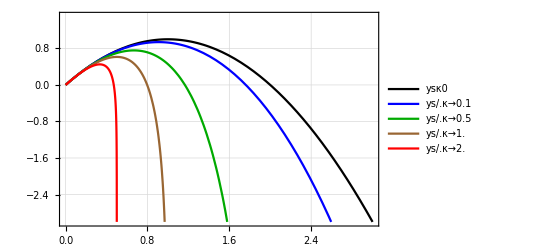

```mathematica
Plot[{Limit[ys,κ->0],ys/.κ->0.1,ys/.κ->0.5,ys/.κ->1.0,ys/.κ->2.0},{xs,0,3},
PlotStyle->{Black, Blue, Darker@Green,Brown,Red},PlotRange->{{0,3},{-3,1.5}},GridLines->Automatic,Frame->True,
PlotLegends->"Expressions"]
```

本题繁琐处之一在于求解非齐次运动方程：(ⅆ v⃗)/ⅆt+(v⃗)/τ=g⃗

对二维问题，有时利用复数，可将问题简化为齐次方程。

初始条件的复数表示：(r̃)_0=0,   (ṽ)_0=v_0 ⅇ^(ⅈ ϕ_0),    记得复数表示中 ⅇ^(ⅈ ϕ) 对应于 (ê)_ρ，ⅈ ⅇ^(ⅈ ϕ) 对应于 (ê)_ϕ

速度(二维矢量)  v⃗  的复数表示：  ṽ=v ⅇ^(ⅈ ϕ) ；         重力加速度 的复数表示：  g̃=-ⅈ g   (沿 -(ê)_y 方向)

运动方程：(ⅆ v⃗)/ⅆt+(v⃗)/τ=g⃗   ⟹^复数形式    (ⅆ ṽ)/ⅆt+(ṽ)/τ=g̃=-ⅈ g        重力沿 -(ê)_y，复数形式有个 -ⅈ

从而：(ⅆ ṽ)/ⅆt=g̃-(ṽ)/τ      ⟹    (ⅆ ṽ)/(ṽ-g̃ τ)=-ⅆt/τ    ⟹   ∫_((ṽ)_0)^(ṽ) (ⅆ ṽ)/(ṽ-g̃ τ)=-∫_0^t ⅆt/τ

(⟹   ((ln(ṽ-g̃ τ))^)_|)_((ṽ)_0)^(ṽ)=-t/τ        ⟹     ṽ-g̃ τ=((ṽ)_0-g̃ τ)ⅇ^(-t/τ)         ⟹      ṽ=((ṽ)_0-g̃ τ)ⅇ^(-t/τ)+g̃ τ

⟹     r̃=(r̃)_0+∫_0^t ṽ ⅆt=[-((ṽ)_0-g̃ τ)τ ⅇ^(-t/τ)+g̃ τ t]_0^t=((ṽ)_0-g̃ τ)τ(1- ⅇ^(-t/τ))+g̃ τ t

区分虚实部：  r̃=(v_0 τ cos α (1- ⅇ^(-t/τ)))_(x(t))+ⅈ [(v_0 τ sin α+g τ)τ (1- ⅇ^(-t/τ))-g τ t]_(y(t))            运动轨迹

求解过程回避了非齐次微分方程的求解，再次体会复数的妙用（可惜多仅适用于二维）。

你明白为什么哈密顿会如此痴迷于四元数了吗？

例题 1.2.03

圆环位于竖直平面内，环上一颗串珠从与环心等高的位置 A （如图）

零初速下滑至最低点刚好静止。求圆环摩擦系数。

解：

已知轨道，用自然坐标。
A 点为起点，自然坐标 s=R θ
速率 v=R θ̇,  
加速度的两个分量
    {a_τ=v̇=R θ^(..)
a_n=v^2/R=R(θ̇)^2
牛顿定律：
     {m R θ^(..)=m g cos θ-f
m R (θ̇)^2=N-m g sin θ     -Graphics-

利用 f=μ N 消去 N，得到  θ 的微分方程：R ( θ^(..)+μ(θ̇)^2)=g (cos θ-μ sin θ)               (†)

——  非线性常微分方程！

利用   θ^(..)=(ⅆ θ̇)/ⅆt=(ⅆ θ̇)/ⅆθ ⅆθ/ⅆt=θ̇(ⅆ θ̇)/ⅆθ=1/2(ⅆ(θ̇)^2)/ⅆθ,      记住       θ^(..)=1/2(ⅆ(θ̇)^2)/ⅆθ

微分方程化 (†) 为：(ⅆ(θ̇)^2)/ⅆθ+2μ(θ̇)^2=(2g)/R(cos θ-μ sin θ)

看左边，如果令  Θ(θ)=(θ̇)^2，微分方程化为：

Θ'+2μ Θ=h(θ)≡(2g)/R(cos θ-μ sin θ)          一阶线性非齐次常系数常微分方程

先看齐次方程：Θ'+2μ Θ=0    ⟹       Θ=Θ_0 ⅇ^(-2 μ θ)   ⟹^常数变易法    Θ=ⅇ^(-2 μ θ)Φ(θ)

原微分方程化为：  ⅇ^(-2 μ θ)  Φ'=h(θ ) =(2g)/R(cos θ-μ sin θ)     ⟹      Φ'=ⅇ^(2μ θ)h(θ) ，

以  Φ =ⅇ^(2μ θ)Θ=ⅇ^(2μ θ)(θ̇)^2 代入   Φ'=ⅇ^(2μ θ)h(θ) ，

即        ⅆ/ⅆθ(ⅇ^(2μ θ)(θ̇)^2)_(⏟_Φ)=ⅇ^(2μ θ)(2g)/R(cos θ-μ sin θ)，注意左边是全微分（尽管是非线性的）

注：一阶线性非齐次常系数常微分方程  y'+μ y =f(x)  标准解法：两边同乘以 ⅇ^(μ x)左边构成全微分

两边同时积分并主要到 t=0 时 θ=(θ̇)^=0，可得

ⅇ^(2μ θ)(θ̇)^2=(2g)/R∫_0^θ (cos θ-μ sin θ)ⅇ^(2μ θ)ⅆθ

右边的积分还是用 \[MathematicaIcon] Mathematica 计算吧，就如用计算器

```mathematica
Simplify[Exp[-2μ θ]Integrate[(Cos[q]-μ Sin[q])Exp[2μ q],{q,0,θ}]];
TraditionalForm[%]
```

(-2 μ^2 sin(θ)-3 μ ⅇ^(-2 θ μ)+3 μ cos(θ)+sin(θ))/(4 μ^2+1)

所以我们得到：(θ̇)^2=(2g[3 μ( cos θ-ⅇ^(-2μ θ))+(1-2 μ^2) sin θ])/((1+4 μ^2)R)

很复杂？幸亏只需求出 μ ，而非求 θ 与时间的关系。

在 θ=π/2 时，θ̇=0，代入上方程得：(1-2 μ^2)-3μ ⅇ^(- μ π)=0

求解这个超越方程，常用迭代法：μ=√((1-3μ ⅇ^(- μ π))/2)

画图可知，方程虽然貌似复杂，但函数是单调的，容易数值求解。

用 \[MathematicaIcon] Mathematica 计算，不费吹灰之力。

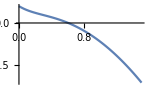

{μ→0.603342}

```mathematica
Plot[(1-2 μ^2)-3μ ⅇ^(- μ π),{μ,0,1.5},ImageSize->150]
FindRoot[(1-2 μ^2)-3μ ⅇ^(- μ π),{μ,0}]
```

例题 1.2.04

质量 m 半径 R 的光滑半球平面朝下置于光滑水平台面，

质点 m 自球面顶端无初速下滑。求质点脱离球面的位置

解：

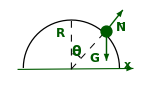
难点在于半球面非固定，会向左滑动
            两种情况，哪种质点更早脱落？
最直接的解法是列出运动方程
对半球有：
    m x^(..)=-N sin θ                                                       (a)
对质点有：
   {m(R θ^(..)+x^(..)cos θ)=m g sin θ                          (b)
m(R (θ̇)^2-x^(..)sin θ)=m g cos θ-N             (c)   -Graphics-

其中利用：  a⃗'=a⃗-(a⃗)_牵连   ⟹     a⃗=a⃗'+(a⃗)_牵连=a⃗'+a⃗''

式 (b) 来自质点切向加速度    a_τ= R θ^(..)+a_τ^(′′)，    a''_τ=x^(..)cos θ     牵连加速度 x^(..)的切向分量

式 (c) 来自质点法向加速度    a_n= R (θ̇)^2+a_n^(′′)， a''_n=-x^(..)sin θ   牵连加速度 x^(..)的法向分量

现在关注 θ 及其时间导数，因而要消去 N 及 x^(..)

以式 (c) 求出

N=m g cos θ-m(R (θ̇)^2-x^(..)sin θ)           代入式 (a) 求得 x^(..)

x^(..)=(-g cosθ  sinθ+R sinθ (θ̇)^2)/(1+sin^2 θ)                 将此式代入 (b) 即得 θ 及其时间导数的方程

(3 -cos 2θ)R θ^(..) +R (θ̇)^2 sin 2 θ=4 g sin θ               (d)

其实这几步挺繁琐，幸亏有 \[MathematicaIcon] Mathematica

```mathematica
Quit
```

```mathematica
eq1=m xdd+Nf sinθ;
eq2=m(R θdd+xdd cosθ)-m g sinθ;
eq3=m(R θd^2-xdd sinθ)-m g cosθ+Nf;
sim={sinθ->Sin[θ],cosθ->Cos[θ]};
```

```mathematica
sol1=Solve[eq3==0,Nf]
eq1s=eq1/.sol1[[1]];
sol2=Solve[eq1s==0,xdd]
eq2s=eq2/.sol2[[1]];
Simplify[Together[eq2s]];
FullSimplify[Numerator[%]/.sim]
```

{{Nf→cosθ g m+m sinθ xdd-m R θd^2}}

{{xdd→(-cosθ g sinθ+R sinθ θd^2)/(1+sinθ^2)}}

1/2 m (3 R θdd-R θdd Cos[2 θ]-4 g Sin[θ]+R θd^2 Sin[2 θ])

(3 -cos 2θ)R θ^(..) +R (θ̇)^2 sin 2 θ=4 g sin θ               (d)

接着，还需要一点小技巧，记得常用的公式   θ^(..)=(ⅆ θ̇)/ⅆt=(ⅆ θ̇)/ⅆθ ⅆθ/ⅆt=1/2(ⅆ(θ̇)^2)/ⅆθ，代入式 (d)

得： (3 -cos 2θ)R θ^(..) +R (θ̇)^2 sin 2 θ=4 g sin θ     ⟹^(θ^(..) =1/2(ⅆ(θ̇)^2)/ⅆθ)      (2-cos^2 θ)/2(ⅆ(θ̇)^2)/ⅆθ+(θ̇)^2 sin θ cos θ=(2g)/R sin θ

还是令 Φ=(θ̇)^2     方程化为   (2-cos^2 θ)/2 ⅆΦ/ⅆθ+Φ sin θ cos θ=f(θ)=(2g)/R sin θ

又是一个非齐次线性微分方程，但这次不是常系数

先看齐次方程：(2-cos^2 θ)/2 ⅆΦ/ⅆθ+Φ sin θ cos θ=0   ⟹    ⅆΦ/Φ=-(2 sin θ cos θ)/(2-cos^2 θ) ⅆθ

⟹    Φ=Φ_0/(2-cos^2 θ)     ⟹^常数变易法    Φ=(Θ(θ))/(2-cos^2 θ)        ⟹^(带入方程 (1.EquationNumbered))       ⅆΘ/ⅆθ=(4g)/R sin θ

```mathematica
Quit
```

```mathematica
Φ=Θ[θ]/(2-Cos[θ]^2);
eq=(2-Cos[θ]^2)/2 D[Φ,θ]+Φ Sin[θ]Cos[θ]==(2g)/R Cos[θ];
Simplify[eq]
```

(4 g Cos[θ])/R==Θ'[θ]

Θ=(4g)/R(1-cos θ)      ⟹   Φ=(θ̇)^2=(Θ(θ))/(2-cos^2 θ)=(4g)/R(1-cos θ)/(2-cos^2 θ)                       (e)

质点离开半球时刻，N=0   ⟹^(利用本题式 (a))   x^(..)=0

这个时刻，我们很自然地想到要将刚求到的 (θ̇)^2 代入 (c) 式：m(R (θ̇)^2-x^(..)sin θ)=m g cos θ-N

可得            (⟹^(N=0 ,  x^(..)=0))_(式 (e)的(θ̇)^2)            4(1-cos θ)/(2-cos^2 θ)=cos θ

求得 cos θ=√3-1.     （若半球面固定，则 cos θ=2/3）

```mathematica
Solve[4(1-c)==c(2-c^2),c]
```

{{c→2},{c→-1-√3},{c→-1+√3}}

●   本题的另一种解法是利用动量的 x 分量守恒，机械能守恒

对质点： {v_(2x)=R(θ̇)^cos θ+(ẋ)^
v_(2y)=-R(θ̇)^sin θ 动量守恒：m v_(2x)+((m ẋ)_半球动量)^=0

⟹   ẋ=-(R(θ̇)^cos θ)/2=-v_(2x)

机械能守恒：1/2(m v_(2x)^2+m v_(2y)^2+m (ẋ)^2+m g R cos θ)=m g R

ẋ,v_(2x), v_(2y)   代入上式可得：(θ̇)^2=(8g)/R(1-cos θ)/(3-cos2θ)=(4g)/R(1-cos θ)/(2-cos^2 θ)

将暗紫色的三个等式写入代码即可求得：

```mathematica
eq=1/2(m v2x^2+m v2y^2+m xd^2)+m g R Cos[θ]-m g R;
xd=-(R θd Cos[θ])/2;
v2x=-xd;
v2y=-R θd Sin[θ];

eqs=FullSimplify[eq];
Solve[eqs==0,θd];
FullSimplify[θd^2/.%[[1]]]
```

(8 g (-1+Cos[θ]))/(R (-3+Cos[2 θ]))

例题 1.2.05

半球碗内壁光滑，半径为 R．小珠初始位置距碗口高度差为 h，

具有水平初速 v_0．欲使小珠不从碗口飞出，v_0 最大值为多少？

解：

总可以从运动方程出发
写出球坐标下的速度、加速度
{v_r=ṙ=0
v_θ=r θ̇
v_ϕ=r ϕ̇ sin θ    v^2=r^2(θ̇)^2+r^2(ϕ̇)^2 sin^2 θ
a_α=(((1/h_α[ⅆ/ⅆt∂/(∂(q̇)_α)((v⃗)^2/2)- ∂/(∂q_α)((v⃗)^2/2)])^)_)^
{a_θ=r θ^(..)+2 ṙ θ̇-r(ϕ̇)^2 sin θ cos θ
a_ϕ=1/(r sin θ)ⅆ/ⅆt(r^2 ϕ̇ sin^2 θ)   -Graphics-

牛顿定律：{m a_θ=m R(θ^(..)-(ϕ̇)^2 sin θ cos θ)=m g sin θ         (a)
m a_ϕ=m 1/(R sin θ)ⅆ/ⅆt(R^2 ϕ̇ sin^2 θ)=0                   (b)        暗紫色项为守恒量

飞出碗口显然是由于 v_θ=r θ̇  导致，
        故先消去  ϕ̇，以便研究 θ 的方程
由式 (b) 得：ⅆ/ⅆt(R^2 ϕ̇ sin^2 θ)=0    ⟹
  R^2 ϕ̇ sin^2 θ=R v_ϕ sin θ  不变，等于初始值-Graphics-

故： R^2 ϕ̇ sin^2 θ=R v_0 sin θ_0=R v_0 (√(R^2-h^2))/R=v_0 √(R^2-h^2)     参加上图几何关系

⟹      ϕ̇=(v_0 √(R^2-h^2))/(R^2 sin^2 θ)   代入式 (a) 并利用 θ^(..) 凑成全微分 1/2(ⅆ(θ̇)^2)/ⅆθ=θ^(..)

得到关于 θ 的方程

ⅆ/ⅆθ((R(θ̇)^2)/2)-[((R^2-h^2)v_0^2 cos θ)/(R^3 sin^3 θ)+g sin θ]_(对这项积分，凑成全微分)=0

得：ⅆ/ⅆθ[(R(θ̇)^2)/2-((R^2-h^2)v_0^2)/(2 R^3 sin^2 θ)+g cos θ]=0

⟹   [(m R^2(θ̇)^2)/2+(m(R^2-h^2)v_0^2)/(2 R^2 sin^2 θ)+m g R cos θ] 不变，等于初始值：1/2 m v_0^2-m g h

即：(m R^2(θ̇)^2)/2+(m(R^2-h^2)v_0^2)/(2 R^2 sin^2 θ)+m g R cos θ=1/2 m v_0^2-m g h

飞出碗口的最小速度对应于：在 θ=π/2 时，θ̇=0，代入上式得

(m(R^2-h^2)v_0^2)/(2 R^2)=1/2 m v_0^2-m g h     ⟹   v_0=R √((2g)/h)

●   本题的另一种解法是利用角动量的 z 分量守恒和机械能守恒

{v_r=ṙ=0
v_θ=r θ̇
v_ϕ=r ϕ̇ sin θ   ⟹   {v⃗=r θ̇ (e⃗)_θ+r ϕ̇ sin θ  (e⃗)_ϕ
N⃗=-N (e⃗)_r,     N⃗·v⃗=0，机械能守恒

力矩  τ⃗=r⃗×(N⃗+G⃗)=r (e⃗)_r×(-N (e⃗)_r-m g(e⃗)_z)=m g r (e⃗)_ϕ，   角动量 z 分量守恒

机械能：                  E= 1/2 m (v⃗)^2+ m g R cos θ

角动量 z 分量：  L_z= (e⃗)_z·[R (e⃗)_r×m v⃗]
=m R^2 (e⃗)_z·[ (e⃗)_r×(θ̇ (e⃗)_θ+ϕ̇ sin θ  (e⃗)_ϕ)]=m R^2 ϕ̇ sin^2 θ

其中利用了： (e⃗)_r× (e⃗)_θ= (e⃗)_ϕ⊥(e⃗)_z
(e⃗)_r×(e⃗)_ϕ=-(e⃗)_θ,     (e⃗)_z·(e⃗)_θ=-sin θ

{ 机械能守恒                
 1/2 m R^2((θ̇)^2+(ϕ̇)^2 sin^2 θ)+m g R cos θ=1/2 m v_0^2-m g h
角动量 z 分量守恒                            
m R^2 ϕ̇ sin^2 θ=m v_0 R sin θ_0
          θ_0 是初始极角，sin θ_0=(√(R^2-h^2))/R  见右图

将上方程组第二式求出 ϕ̇=(v_0 √(R^2-h^2))/(R^2 sin^2 θ)  代入第一式即得关于 θ 的方程

(m R^2(θ̇)^2)/2+(m(R^2-h^2)v_0^2)/(2 R^2 sin^2 θ)+m g R cos θ=1/2 m v_0^2-m g h

利用 θ=π/2 时，θ̇=0 可得： v_0=R √((2g)/h)

\[FreakedSmiley]  知 v_0≠0，试问运动过程中小珠是否会经过碗底 θ=π？（No. 违反机械能守恒或角动量的 z 分量守恒）

例题 1.2.06

求解半径 r 的小球在半径 R 的半球形固定大碗内的小角度纯滚动

解： 如图  （本题解法方程 (b) 和 (c) 的正负号有点变化）

-Graphics-   -Graphics-

运动方程，记 ϕ 为小球无滑动滚动转过的角度（设小球在底部时，a 与 A 重合）

对小球，质心动量方程：                  f-m g sin θ=m(R-r)θ^(..)     (a)

小球绕直径转动的角动量方程：  I ϕ^(..)=2/5 m r^2 ϕ^(..)=-f r              (b)    其中 ϕ 为 oa 与竖直线的夹角即小球转过的角度

接触点不滑动，速度为 0：            (R-r)θ̇-r ϕ̇=0                         (c)

其中：(b)式利用了球绕直径的转动惯量  I=2/5 m r^2

(b) 和 (c)式要注意 ϕ 与 θ 的方向，否则方程会差个负号

θ 与 ϕ 有集合关系：(θ+ϕ) r = θ R      ⟹   也可得到 (c) 式

(c)式对时间求导： (R-r)θ^(..)-r ϕ^(..)=0

再与 (b) 联立求出： f=2/5 m (r-R)θ^(..)     代入 (a)式得：

7/5 m(R-r)θ^(..)+m g sin θ=0                      (d)

θ≪1 时，sin θ≈θ   上式退化为： 7/5 m(R-r)θ^(..)+m g θ=0

从而，来回滚动的角频率：ω=√((5g)/(7(R-r))),   周期  T=(2π)/ω

●   本题的另一种解法是机械能守恒

因为小球受重力 G⃗、支撑力 N⃗ 和摩擦力 f⃗ 作用做纯滚动

小球与大碗的接触点无位移， N⃗ 和 f⃗ 不做功，故机械能守恒。

记得  Konig 定理：质点系总动能等于质心动能 T_o 与内动能 T_I 之和

动能：T_o=1/2 m[(R-r) θ̇]^2,   T_I=1/2 I ω^2=1/2×2/5 m r^2(ϕ̇)^2

势能：V=m g h=m g (R-r)(1-cos θ)

机械能：E=T+V  ⟹  利用纯滚动条件式 (c) ：  (R-r)θ̇+r ϕ̇=0

得：     E=(1/2(m(R-r))^2 (θ̇)^2)_T_o+(1/5 m(R-r)^2 (θ̇)^2)_T_I+(m g (R-r)(1-cos θ))_V

整理得运动方程：m(R-r)[7/10(R-r)(θ̇)^2+g(1-cos θ)]=E

两边同时对 t 求导得： 7/5(R-r)θ^(..)+ g sin θ=0      与上述式 (d) 一致

●   无滑动条件下的角速度关系

如图，设大小球半径为 R 与 r
          大小球球心分别为 O 与 o
设小球在底部时，a 与 A 重合
     某时刻，小球转过 ϕ，如图
     两球心连线与 y 轴成 θ 角
因无滑动，接触点 B 的速度为
                v_B=0
而  v_B=v_o-ϕ̇ r，r 为小球半径
  小球球心速度 v_o= (R-r)θ̇
  故  v_B=0   ⟹   (R-r)θ̇=r ϕ̇-Graphics-

或者：从 A 到接触点 B 的一段弧长为   R θ=(ϕ+θ)r   ⟹   (R-r)θ=r ϕ

例题 1.2.07

悬链线：两端固定匀质软链在重力场中静平衡的曲线形状

解： 如图软链上从 x 到 x+ⅆx 的一小段

对这一小段列静力学方程
设软链的张力为 T=T_x(e⃗)_x+T_y(e⃗)_y
{T_x(x+ⅆx)-T_x(x)=0
T_y(x+ⅆx)-T_y(x)-η gⅆs=0
   其中：η 为软链的线质量密度
     弧长 ⅆs=√((ⅆx)^2+(ⅆy)^2)
                       =√(1+(y^′)^2)ⅆx
T_x(x+ⅆx)-T_x(x)=0  
   ⟹   (ⅆ T_x)/ⅆx=0  ⟹ T_x(x)=T_0

T_y/T_x=tan θ    ⟹   T_y=T_0 y'

故：T_y(x+ⅆx)-T_y(x)-η gⅆs=0   ⟹   ⅆ(T_0 y')=η g √(1+y'^2)ⅆx

从而 y 满足微分方程： (ⅆ y')/(√(1+(y^′)^2))=ⅆx/C_1           其中 C_1=T_0/(η g)，注意 T_0 尚未知

积分：arcsinh y'=(x-C_2)/C_1   ⟹   y'=sinh(x-C_2)/C_1   ⟹   y=C_1 cosh(x-C_2)/C_1+C_3

三个待定参数 C_1, C_2, C_3 可以由软链两端 A, B  的位置坐标及链长 l 确定

{y_A=C_1 cosh(x_A-C_2)/C_1+C_3
 y_B=C_1 cosh(x_B-C_2)/C_1+C_3
l=C_1 sinh(x_B-C_2)/C_1-C_1 sinh(x_A-C_2)/C_1

其中利用了：
   l=∫ⅆs=∫_x_A^x_B √(1+(y^′)^2)ⅆx
       =∫_x_A^x_B √(1+sinh^2(x-C_2)/C_1)ⅆx     记得   {cosh^2 x-sinh^2 x=1
ⅆsinh x=cosh x ⅆx
(=C_1 sinh(x-C_2)/C_1|)_x_A^x_B

软链悬挂形状动态图

例题 1.2.08

内壁光滑的长直细管在水平面内绕一端 O 以匀角速度 ω 转动。管内有

一原长 l、质量 M、劲度系数 k 的张紧弹性绳（松弛时匀质），一端固

定于 O，另一端自由，整体相对管静止。求绳子伸长量与角速度的范围。

解：

背景知识：

位移：由于受惯性离心力的作用，弹性绳在形变前距 O 点 x 处的点被拉伸至 r(x)，

r(x)=x+u(x)，其中 u(x) 称为位移

相对伸长：考虑弹性绳上的一小段（在形变前距 O 点 x 处到 x+ⅆx 的一小段）

形变前这一小段的两端分别位于 x 和 x+ⅆx，如图绿色所示，

形变后，这两端分别位于 r(x)=x+u(x) 与 r(x+ⅆx)=x+ⅆx+u(x+ⅆx) 。

形变前这一小段的长度为：ⅆ l_0=x+ⅆx-x=ⅆx，

形变后这一小段的长度为：ⅆl=r(x+ⅆx)-r(x,t)=ⅆx+ⅆu，

形变导致的伸长为：Δ l=ⅆl-ⅆ l_0=ⅆu    （注意弹性绳只有伸长才有意义）

由于弹性绳的形变导致形变前距 O 点 x 处的一小段（长度微元）的

相对伸长为：(Δ l)/(ⅆ l_0)=ⅆu/ⅆx

Hooke 定律：在弹性限度内，应力（单位截面积的力）与应变（相对伸长）成正比，

比例系数称为杨氏模量 Y>0

就是那个跟牛顿过不去的虎克，牛虎之争。

以至于牛顿说“站在巨人的肩膀上”，

暗指自己的成就没虎克啥事，因为虎克个子矮。

——  果然聪明绝顶，骂人不带脏字

杨氏模量  vs 劲度系数

假设一根原长度 l 的弹性绳受拉力 F 时，伸长到 l'=l+ε

由弹簧劲度系数 k 的定义可知  F=k (l'-l)=k ε

从 Hooke 定律来看，考虑弹性绳从 x 和 x+ⅆx 一小段

(在它的左端 x，它受到拉力（向左）为  F_x=Y S ⅆu/ⅆx|)_x

(在它的右端 x，它受到拉力（向右）为  F_(x+ⅆx)=Y S ⅆu/ⅆx|)_(x+ⅆx)

注：虎克定律建立了相对伸长和应力的关系，正如牛顿第二定律

从相对伸长即可判断那一端收到多大 的力，正如从 a 也可求得 F 一样。

((绳子不动，故 F_(x+ⅆx)-F_x=Y S [ⅆu/ⅆx|)_(x+ⅆx)-ⅆu/ⅆx|)_x]=0

即： (ⅆ^2 u)/(ⅆ x^2)=0   ⟹  u=a x+ b，考虑到边界条件：u|_(x=0)=0
u|_(x=l)=ε

(可得：u=ε/l x     ⟹  在绳子右端： F=Y S ⅆu/ⅆx|)_(x=l)

⟹     F=Y S  ε/l=k ε       ⟹     Y^S=k l

(相同材料弹簧，长度加倍，劲度系数 k 如何变，k 与 Y 哪一个参数更基本？)

回归本题

考虑弹性绳从 x 和 x+ⅆx 一小段，
如图，于是有：

((F_x-F_(x+ⅆx)=Y S [ⅆu/ⅆx|)_x-ⅆu/ⅆx|)_(x+ⅆx)]=r ω^2 ⅆm=r ω^2 M/l ⅆx>0        提供向心加速度

或者，在旋转坐标中理解为合力 F_x-F_(x+ⅆx) 拉住 x 到 x+ⅆx 这一小段，以免被离心力甩出

即：-(Y S)_(k l)(ⅆ^2 u)/(ⅆ x^2)=r ω^2 M/l     ⟹    (ⅆ^2 u)/(ⅆ x^2)+κ^2 r=0，其中  κ=ω/l √(M/k)

记得：r=x+u   ⟹   (ⅆ^2 u)/(ⅆ x^2)=(ⅆ^2 r)/(ⅆ x^2)   ⟹    (ⅆ^2 r)/(ⅆ x^2)+κ^2 r=0

可解得：r=A cos(κ x+φ)    ⟹    u=r-x=A cos(κ x+φ)-x

利用：{(u|)_(x=0)=0
((F_l=0)_自由端=Y S ⅆu/ⅆx|)_(x=l)  确定参数 A, φ， 可得：u=(sin κ x)/(κ cos κ l)-x

(绳子伸长量：u^|)_(x=l)=((tan κ l)/(κ l)-1) l，其中： κ=ω/l √(M/k)

角速度 ω 的范围？

我们上述所有讨论建立在两个基础：

{弹性限度：u 与 ⅆu/ⅆx 都不宜太大
对弹性绳应用Hooke定律，需要 ⅆu/ⅆx≥0 （弹性绳只能伸长，不同于弹性杆）

而   ⅆu/ⅆx=(cos κ x)/(cos κ l)-1    注意 x∈[0,l],    (cos κ x)/(cos κ l)≥1  的条件是   κ l<π/2，但 κ=ω/l √(M/k)

故：ω<π/2 √(k/M)=ω_0，          ω_0=π/2 √(k/M) ,      κ=ω/ω_0 π/(2l)=η/l π/2,       η=ω/ω_0

●    这里没考虑弹性限度限制，当 ω 接近于 ω_0 时，ⅆu/ⅆx 在 x≪l 时会很大，突破弹性限度。

如下图，当 κ l=(9π)/20 时，在 x=0 附近，相对伸长达 0.3，无法保证Hooke定律适用。

●    思考：假设Hooke定律仅在相对伸长小于 20%成立，试求角速度的范围。

下图显示在 η=ω/ω_0=0.4 时，x=0 附近的相对伸长需要 20% 以上才能拉住绳子。

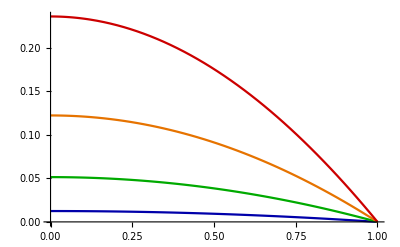

```mathematica
tbl=Table[η,{η,0.1,0.4,0.1}] ;     (*   η=ω/Subscript[ω, 0],   l=1    *)
pdu2pdx=Cos[π/2 η x]/Cos[π/2 η]-1;
Plot[{pdu2pdx/.η->0.1,pdu2pdx/.η->0.2,pdu2pdx/.η->0.3,pdu2pdx/.η->0.4},{x,0,1},
            PlotStyle->{Darker[Blue],Darker[Green],Darker[Orange,0.1],Darker[Red,0.2]}]
```

(若长直细管以 ω 转动，x=0 端的拉力须达到   Y S ⅆu/ⅆx|)_(x=0)= (Y S)/(cos (ω/ω_0 π/2))-Y S 才能拉住绳子。

当 ω→ω_0 时，假设 Hooke 定律依然成立，则 x=0 端拉力需要无穷大才能拉住绳子。

考虑到超出弹性范围的恢复力力通常比 Hooke 定律给出的力小，这时绳子将被甩断。

## § 1.3 变质量体系

如果质点系其中质点或体系质量随时间改变，则称之为变质量体系。（注意对经典体系，质量不随速度改变）

常见的变质量体系有

增质量：主体吸附物质，如形成中的雨滴，ṁ>0

减质量：主体排放物质，如发射中的火箭，ṁ<0

如图显示一个增质量体系质量增加过程

-Graphics-          黄色部分称为“主体”
蓝色部分称为“进出物质”

因此，从 t 到 t+ⅆt，动量改变量（符号意义见图）

ⅆ P⃗=m' v⃗'-(m v⃗+u⃗ ⅆm)=(m' v⃗'-m v⃗)_(ⅆ(m v⃗))-u⃗ ⅆm=ⅆ(m v⃗)-u⃗ ⅆm

整体动量变化来自外力，与进出物质和主体间的内力无关，故

(ⅆ P⃗)/ⅆt=(ⅆ(m v⃗))/ⅆt-u⃗ ⅆm/ⅆt=m(ⅆ v⃗)/ⅆt-(u⃗-v⃗)ⅆm/ⅆt=F⃗      或：

ⅆ(m v⃗)=F⃗ ⅆt+u⃗ⅆm

以上 (1.EquationNumbered) 式可理解为：

开放体系动量变化来自两方面：外力导致动量转移；物质流动伴随动量输运。

动力学方程还可以写成

m(ⅆ v⃗)/ⅆt=F⃗+(u⃗-v⃗)ⅆm/ⅆt               Mischelski 方程（密舍尔斯基方程）

(v⃗-u⃗)ⅆm/ⅆt     理解为主体对进出物质ⅆm 的冲力（使之动量发生改变），

(u⃗-v⃗)ⅆm/ⅆt     理解为进出物质ⅆm 对主体的冲力。

思考：为何作如此理解？  (v⃗-u⃗) 是在 ⅆm 上看，m 以此速度撞击 ⅆm，类似理解 (u⃗-v⃗)ⅆm/ⅆt

因而(1.EquationNumbered)式表明

封闭主体受外力和进出物质施加的冲力作用，导致其速度变化（牛顿第二定律）

●  实际上，并不是非要记住 Mischelski 方程不可，临时推导一下，物理意义更明确（参见以下例题）

思考：理解为牛顿第二定律时， (1.EquationNumbered) 式貌似有个 paradox

一方面， (u⃗-v⃗)ⅆm/ⅆt 可理解为进出物质ⅆm 对主体的冲力， (1.EquationNumbered) 式理解为“牛二”没问题

另一方面， (u⃗-v⃗) 也可理解为在主体上看，进出物质的速度，

因而第二项似乎是，在主体上看，进出物质单位时间给予主体的冲量。

那么，(1.EquationNumbered) 式是在实验室上看的牛二，还是主体物质上看的牛二？后者未必是惯性系。（力不因参考系而改变）

另一种理解：在主体上看：F⃗ 是外力，(u⃗-v⃗)ⅆm/ⅆt 为进出物体撞击力，-m(ⅆ v⃗)/ⅆt 为惯性力，三者之和为 0

例题 1.3.01

定滑轮轻绳一端悬重物 M，另一端系初始时全部静止于地面，

线密度为 η 的长软链．求软链提升的最大高度

解：

地面软链被提起前  u=0
对重物 M 和悬链部分
           列出动力学方程：
{M (ⅆ Ẋ)/ⅆt=M g-T
(ⅆ(m ẋ))/ⅆt=(ⅆ(η x ẋ))/ⅆt=T-η g x
第二个方程来自 u⃗=0 的(1.EquationNumbered) 
也可临时导出，见右。
 二者之和消去 T 得
ⅆ^/ⅆt_[(M+η x)ẋ]=M g-η g x    (†)
这里利用了：Ẋ=ẋ
             为什么不是  Ẋ=- ẋ      以空中 x 段为研究主体
在 t 时刻，动量为
       m v=(η x) ẋ
在 t+ⅆt 时刻，动量为
       (m+ⅆm)(v+ⅆv)
  =(η x+η ⅆx)(ẋ+ⅆ ẋ)
受力的冲量
   (T-η g x)ⅆt
从而
(η x+η ⅆx)(ẋ+ⅆ ẋ)-(η x) ẋ
   =(T-η g x)ⅆt
即：
η ẋ ⅆx+η xⅆ ẋ=(T-η g x)ⅆt
        (ⅆ(η x ẋ))/ⅆt=T-η g x

利用：ⅆ/ⅆt=ẋ ⅆ/ⅆx， 方程 (†)两边同乘以(M+η x)得：

(M+η x)ẋ ⅆ/ⅆx[(M+η x)ẋ]=(M^2-η^2 x^2)g，    两边同积分 ∫_0^x ⅆx

1/2(M+η x)^2(ẋ)^2=(M^2-1/3 η^2 x^2)g x     其中利用了 x=0 时 ẋ=0

软链提升的最大高度 x_max，这时对应于 ẋ=0，故

x_max=(√3 M)/η          （另一个解是 x=0 ）

这时 m_chain g=η x_max g=√3 M g>M g，软链将回落。

那么，软链能回落至初始位置吗？

物理直觉告诉我们，大概率不能回落至初始位置。为什么？

先来看结果 —— 能量被耗散了。

软链提升到最大高度 x_max 时与初始时刻相比，机械能的变化

同是零速，势能之差为：(η x_max)_m g 1/2 x_max-M g x_max    ⟹^(代入 x_max)   -(M^2 g)/(2η)(2 √3-3)

其中左边的第一项为软链势能的增加，第二项为重物势能之减小

重物在下降时，体系的势能就减小了，故只能喟叹“回不去的故乡，到不了的远方”。

思考：那么，能量在什么时候被耗散？

软链微元被拉起时实际上等价于速度 v 与 0 的两物体的完全非弹性碰撞，动量守恒，能量不守恒。

那么，重物能回到什么高度？

只要悬链足够软，链微元 ⅆx 落到地面时，可以看作对悬链部分无冲击，

这样，就相当于链微元落地时速度仍然是 ẋ，撞击发生在链微元 ⅆx 和地面之间

微元 ⅆx 受地面冲击后，速率才降为零。机械能耗散为热能。

也就是，下落时，能量又再一次被耗散为热能。

因此，应该用 u⃗=v⃗ 时的 Mischelski 方程：m(ⅆ v⃗)/ⅆt=F⃗+(u⃗-v⃗)ⅆm/ⅆt

这时悬链动力学方程变为

η x(ⅆ ẋ)/ⅆt=T-η g x      联立重物的方程：  M (ⅆ Ẋ)/ⅆt=M g-T

依然利用 Ẋ=ẋ 及 ⅆ/ⅆt=ẋ ⅆ/ⅆx 可得：ẋ(ⅆ ẋ)/ⅆx=((M-η x)g)/(M+η x)

左右两边同积分：∫_0^(ẋ) ⅆ ẋ  和∫_x_max^x ⅆx， 并记得 x=x_max 时  ẋ=0，可解得

1/2(ẋ)^2=(2g M)/η ln (M+η x)/(M+η x_max)+g(x_max-x)                     (a)

因为有能量损耗，不可能落到 x=0，即：x=0, ẋ=0 代入不满足方程 (a)。

假设落到 x_min 时，ẋ=0

由此可得 ：(2g M)/η ln (M+η x_min)/(M+η x_max)+g(x_max-x_min)=0

以 x_max=(√3 M)/η 代入，得：2 ln (1+η x_min/M)/(√3+1)+√3- (η x_min)/M=0

解得：x_min=0.412 M/η>0   （借助 Mathematica 数值求解，见下）

“日暮苍山远”，软链只能回落至 x_min，回不到初始位置。

可以证明，到达 x_min 时，能量比在 x_max 时又减少了。

```mathematica
eq=2Log[(1+x)/(√3+1)]+√3-x;
FindRoot[eq==0,{x,0}]
```

{x→0.412096}

思考：上升和下落两个过程，能量的耗散有什么不同？上升时能量变软链热能，下降时变软链和地板热能。

```mathematica
eq=x x+xm x+xm xm-3;
sol=Solve[eq==0,x];
sol/.xm->0.4412
```

{{x→-1.90998},{x→1.46878}}

```mathematica
eq=2Log[(1+x)/(1.469+1)]+1.469-x;
FindRoot[eq==0,{x,0}]
```

{x→0.594524}

例题 1.3.02

极小雨滴在均匀静止云雾中由静止开始下落，途中吸附所有与之相遇的雾气

而不断增大，且保持球形．求解雨滴运动。

解：

设雨滴、雾气密度分别为 ρ 和 ρ_0，雨滴半径、速度分别为 r(t) 和 v(t)

雨滴增肥速率：ⅆ(4/3 π r^3 ρ)=π r^2 ρ_0 v ⅆt （设雨滴下落蓝色柱形区的雾气全被吸附）

雨滴 Mischelski 方程：
        m(ⅆ v⃗)/ⅆt=F⃗+(u⃗-v⃗)ⅆm/ⅆt
考虑到雾气 u=0
4/3 π r^3 ρ ⅆv=4/3 π r^3 ρ g ⅆt-vⅆ (4/3 π r^3 ρ)         (†)
     
或者，记不得 Mischelski 方程？
    从 t 到 t+ⅆt 时刻的动量定律来看
     在 t与 t+ⅆt 时刻的动量 P_t 和 P_(t+ⅆt)为
          P_t=m v,    P_(t+ⅆt)= (m+ⅆm)(v+ⅆv)
受力：m g
    (m+ⅆm)(v+ⅆv)- m v=m g ⅆt
 ⟹   ⅆ(m v)=m g ⅆt                                             (a)  
            ⅆm=4π r^2 ρⅆr=π r^2 v ρ_0 ⅆt             (b)

利用  m=(4π)/3 r^3 ρ，方程 (a), (b) 简化为：{ⅆ(r^3 v)=r^3 gⅆt           (‡)
ⅆr=ρ_0/(4ρ) v ⅆt                (#)            注意 方程  (‡)  即为 方程 (†)

⟹   方程 (‡) 和 (#) 相除得：ⅆ(r^3 v)=(4 r^3 ρ g)/(ρ_0 v)ⅆr           ⟹

两边同乘以 r^3 v  得： r^3 vⅆ(r^3 v)=(4 r^6 ρ g)/ρ_0 ⅆr      这下可以两边同时积分了

⟹   1/2(r^3 v)^2=(4 r^7 ρ g)/(7 ρ_0)      ⟹    v=√((8ρgr)/(7 ρ_0))     此式代入上两个方程 (#) 或 (‡)之任意一个

即可 求 r 与时间的关系：ⅆr=ρ_0/(4ρ) v ⅆt    ⟹    ⅆr=ρ_0/(4ρ) √((8ρgr)/(7 ρ_0)) ⅆt

⟹     ∫_0^r dr/(√r)=∫_0^t √((g ρ_0)/(14ρ))ⅆt            ⟹    r=(ρ_0 g t^2)/(56ρ)      ⟹^(利用 (#) 式)       v=(g t)/7,       a=ⅆv/ⅆt=g/7

附：

ⅆ(r^3 v)=(4 r^3 ρ g)/(ρ_0 v)ⅆr    的一般解法：令 r^3 v=Y,   右边对 ⅆr 积分，所以要消去 v，v=Y/r^3

⟹    ⅆY=(4 r^8 ρ g)/(ρ_0 Y) ⅆr      ⟹   YⅆY=(4 r^8 ρ g)/ρ_0 ⅆr    ⟹   Y^2=(2 r^7 ρ g)/(7 ρ_0)   ⟹   v=√((8ρgr)/(7 ρ_0))

## End

##### 例题 1.2.03 验证牛顿方程与拉格朗日方程的等价性

```mathematica
Quit
```

```mathematica
L=1/2 m xd[t]^2+1/2 m(R θd[t] Cos[θ[t]]+xd[t])^2+1/2 m(R θd[t] Sin[θ[t]])^2+m g R(1-Cos[θ[t]]);
eq1=D[D[L,θd[t]],t]-D[L,θ[t]];
eq1=FullSimplify[Expand[eq1/(m R)]/.θ'[t]->θd[t]]/.{θ[t]->θ,xd'[t]->xdd,θd'[t]->θdd};
eq1s=R θdd+xdd Cos[θ]-g Sin[θ];
eq2=D[D[L,xd[t]],t]-D[L,x];
eq2=FullSimplify[eq2/m];
eq2=eq2//.{θ[t]->θ,θ'[t]->θd,θd[t]->θd,xd'[t]->xdd,θd'[t]->θdd};
eq2s=R θd^2-xdd Sin[θ]-g Cos[θ]-xdd/Sin[θ];
```

```mathematica
eq1-eq1s
tmp=Simplify[(eq2+eq2s Sin[θ])];
Simplify[tmp,{eq1==0}]
```

0

0